```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

### J around other cusps

```mathematica
J1=Simplify[MirrorCurveJ2[-27/256,ur]]
```

-((8+9 ur) (512-576 ur+1080 ur^2+81 ur^3)^3)/(19683 ur^8 (64-80 ur+153 ur^2))

```mathematica
ur0=ur/.Solve[64-80 ur+153 ur^2==0,ur]
```

{8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
a1=FullSimplify[Series[J1,{ur,ur0[[2]],10}]];
```

```mathematica
a2=Series[8/153 (5+8 ⅈ √2)+Sum[a[i]q^i, {i,10}], {q,0,10}];
```

```mathematica
a3=Simplify[ComposeSeries[a1, a2]];
```

```mathematica
Series[1728KleinInvariantJ[Log[q]/(2Pi I)], {q,0,10}]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+333202640600 q^5+4252023300096 q^6+44656994071935 q^7+401490886656000 q^8+3176440229784420 q^9+22567393309593600 q^10+O[q]^11

```mathematica
sol=Simplify[Solve[a3-Series[1728KleinInvariantJ[Log[q]/(2Pi I)], {q,0,10}]==0,Array[a,10]]];
```

```mathematica
a3=a2/.First[sol]
```

8/153 (5+8 ⅈ √2)+(2048 (-6976-11369 ⅈ √2) q)/5688387+(16384 (1680185024+3039785485 ⅈ √2) q^2)/1903396862457+(8192 (-5850038733668800-12823968247666619 ⅈ √2) q^3)/636897527543599227+(131072 (623934858062410040896+1730410785263304691583 ⅈ √2) q^4)/213112918588891280945697+(4096 (-32285410263955807669386142400-119216980116040976696010842671 ⅈ √2) q^5)/71309926801947500408520618867+(851968 (225312627148995689010046635702080+1228127125030765062095451239775739 ⅈ √2) q^6)/23861085917126455059195492799705737+(16384 (-13273013073896587641852351287727748975808-136343966552091559733181103371477516558199 ⅈ √2) q^7)/7984181819815600253812463041202336363307+(1048576 (54101480085223225428904679341295683198080704+4531868742473204429610098951898257676160667629 ⅈ √2) q^8)/2671595062910317816528442070679754972862518577+(2048 (360861703099706899184578271967342901387604913880160192-4917997983752467773292580702819657484699438166773971597 ⅈ √2) q^9)/893945095595484354906398529712223491224500203568547+(32768 (-11483946860826203938932458566568074221676732563999415900864+72124473939190344808126337140617564106673048139677657976451 ⅈ √2) q^10)/33235984709144512831064990936170757180235693068475008913+O[q]^11

```mathematica
a3[[3]]
```

{8/153 (5+8 ⅈ √2),(2048 (-6976-11369 ⅈ √2))/5688387,(16384 (1680185024+3039785485 ⅈ √2))/1903396862457,(8192 (-5850038733668800-12823968247666619 ⅈ √2))/636897527543599227,(131072 (623934858062410040896+1730410785263304691583 ⅈ √2))/213112918588891280945697,(4096 (-32285410263955807669386142400-119216980116040976696010842671 ⅈ √2))/71309926801947500408520618867,(851968 (225312627148995689010046635702080+1228127125030765062095451239775739 ⅈ √2))/23861085917126455059195492799705737,(16384 (-13273013073896587641852351287727748975808-136343966552091559733181103371477516558199 ⅈ √2))/7984181819815600253812463041202336363307,(1048576 (54101480085223225428904679341295683198080704+4531868742473204429610098951898257676160667629 ⅈ √2))/2671595062910317816528442070679754972862518577,(2048 (360861703099706899184578271967342901387604913880160192-4917997983752467773292580702819657484699438166773971597 ⅈ √2))/893945095595484354906398529712223491224500203568547,(32768 (-11483946860826203938932458566568074221676732563999415900864+72124473939190344808126337140617564106673048139677657976451 ⅈ √2))/33235984709144512831064990936170757180235693068475008913}

```mathematica
Simplify[Series[(a j+b)/(c j+d)/.{j->1/q+744+aa1 q+aa2 q^2},{q,0,3}]][[3]]
```

{a/c,(b c-a d)/c^2,-((744 c+d) (b c-a d))/c^3,-((b c-a d) ((-553536+aa1) c^2-1488 c d-d^2))/c^4}

```mathematica
Simplify[(a j+b)/(c j+d)/.Solve[{
a/c==8/153 (5+8 ⅈ √2),
(b c-a d)/c^2==(2048 (-6976-11369 ⅈ √2))/5688387,
-((744 c+d) (b c-a d))/c^3==(16384 (1680185024+3039785485 ⅈ √2))/1903396862457,
a d-b c==1
},{a,b,c,d}]]
```

{(72 (908624 ⅈ-1452928 √2+243 (-5 ⅈ+8 √2) j))/(246845200 ⅈ+54784 √2-334611 ⅈ j),(72 (908624 ⅈ-1452928 √2+243 (-5 ⅈ+8 √2) j))/(246845200 ⅈ+54784 √2-334611 ⅈ j)}

```mathematica
Inverse[{{6,-1},{1,0}}]
```

{{0,1},{-1,6}}

```mathematica
-1/(tau-6)
```

-1/(-6+tau)

```mathematica
Simplify[NumeratorDenominator[PicardFuchsP2[el,ur]]/.{el->-27/256}]
```

{((8+9 ur)^2 (768-128 ur+1260 ur^2+4131 ur^3))/2048,(ur (8+9 ur)^3 (64-80 ur+153 ur^2))/4096}

```mathematica
Factor[NumeratorDenominator[PicardFuchsQ2[el,ur]]/.{el->-27/256}]
```

{((8+9 ur) (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/2048,(ur^2 (8+9 ur)^3 (64-80 ur+153 ur^2))/4096}

```mathematica
Factor[16384+32768 ur+73728 ur^2+401760 ur^3+676512 ur^4+334611 ur^5, Extension->Automatic]
```

(8+9 ur) (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4)

```mathematica
Simplify[PicardFuchsP2[el,ur]/.{el->-27/256}]
```

(2 (768-128 ur+1260 ur^2+4131 ur^3))/(ur (8+9 ur) (64-80 ur+153 ur^2))

```mathematica
Simplify[PicardFuchsQ2[el,ur]/.{el->-27/256}]
```

(2 (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/(ur^2 (8+9 ur)^2 (64-80 ur+153 ur^2))

```mathematica
PF[f_,ur_]:=D[f,{ur,3}]+(2 (768-128 ur+1260 ur^2+4131 ur^3))/(ur (8+9 ur) (64-80 ur+153 ur^2))D[f,{ur,2}]+(2 (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/(ur^2 (8+9 ur)^2 (64-80 ur+153 ur^2))D[f,{ur,1}];
```

```mathematica
Simplify[Series[PF[Log[ur]+Sum[a[i]ur^i, {i,1,30}],ur], {ur,0,20}]];
s2=Series[Log[ur]+Sum[a[i]ur^i, {i,1,30}],{ur,0,20}]/.First@Solve[Thread[%[[3,1;;20]]==0],Array[a,20]]
```

Log[ur]-(27 ur^2)/256-(27 ur^3)/128+(2187 ur^4)/131072+(2187 ur^5)/16384+(1366875 ur^6)/8388608-(295245 ur^7)/4194304-(4214031885 ur^8)/17179869184-(98972685 ur^9)/536870912+(641927052459 ur^10)/2748779069440+(138331435095 ur^11)/274877906944+(49684957439733 ur^12)/281474976710656-(25187626531683 ur^13)/35184372088832-(132624450992509047 ur^14)/126100789566373888+(4939250804555067 ur^15)/45035996273704960+(308655712675007143875 ur^16)/147573952589676412928+(2399996726641023939 ur^17)/1152921504606846976-(3791656653113811214161 ur^18)/2361183241434822606848-(6895785518346535409313 ur^19)/1180591620717411303424-(20818733654847363192290619 ur^20)/6044629098073145873530880+O[ur]^21

```mathematica
Simplify[Series[PF[1/2Log[ur]^2+Sum[a[i]ur^i, {i,1,5}]Log[ur]+Sum[b[i]ur^i, {i,1,5}],ur], {ur,0,8}]];
SolveAlways[%[[3,1;;9]]==0, Join[Array[a,5],Array[b,5]]]
```

{}

```mathematica
Simplify[PF[s3,ur]]
```

-81/(64 ur)-2889/512+(189 ur)/4096+(209115 ur^2)/65536+O[ur]^3

```mathematica
Simplify[F1Series2[el,ur,5,0]]
```

{{1/2 el ur^2 (2+4 ur+3 el ur^2+24 el ur^3),-ur/4+(1/16-el) ur^2-1/36 (1+90 el) ur^3-1/64 (-1+24 el+208 el^2) ur^4-1/300 (3-50 el+6450 el^2) ur^5},{2 el ur (1+3 ur+3 el ur^2+30 el ur^3),-1/4+(1/8-2 el) ur-1/12 (1+90 el) ur^2+(1/16-(3 el)/2-13 el^2) ur^3-1/60 (3-50 el+6450 el^2) ur^4},{2 el (1+6 ur+9 el ur^2+120 el ur^3),1/8-ur/6+(3 ur^2)/16-ur^3/5-el^2 ur^2 (39+430 ur)+el (-2-15 ur-(9 ur^2)/2+(10 ur^3)/3)}}

### GPT Frobenius

```mathematica
ClearAll[minPowerFromSeries];
minPowerFromSeries[expr_,u_Symbol,n_Integer]:=Module[{ser},ser=Series[expr,{u,0,n}];
If[Head[ser]===SeriesData,ser[[4]],0]];

ClearAll[linearSolveRules];
linearSolveRules[eqs_List,vars_List]:=Module[{poly,ca,mat,vec,solvec,r},(*turn eqs into linear expressions==0*)poly=(eqs/. Equal->Subtract);
ca=CoefficientArrays[poly,vars];
vec=-Normal[ca[[1]]];
mat=Normal[ca[[2]]];
Which[mat==={}||vars==={},{},Dimensions[mat][[1]]===Dimensions[mat][[2]],solvec=LinearSolve[mat,vec];
Thread[vars->solvec],True,(*overdetermined/rectangular:solve via normal equations*)solvec=LinearSolve[Transpose[mat].mat,Transpose[mat].vec];
Thread[vars->solvec]]];

ClearAll[seriesEqsUpTo];
seriesEqsUpTo[expr_,u_Symbol,n_Integer]:=Module[{kmin},kmin=minPowerFromSeries[expr,u,n];
Table[SeriesCoefficient[expr,{u,0,k}]==0,{k,kmin,n}]];

ClearAll[logSeriesEqsUpTo];
logSeriesEqsUpTo[expr_,u_Symbol,n_Integer,pmax_Integer]:=Module[{ser,poly},ser=Normal@Series[expr,{u,0,n}];
poly=Collect[ser,Log[u]];
Flatten@Table[seriesEqsUpTo[Coefficient[poly,Log[u],p],u,n],{p,0,pmax}]];


(*---main:Frobenius basis for rho^3=0---*)

ClearAll[FrobeniusBasisRho0Triple];
FrobeniusBasisRho0Triple[PFop_,u_Symbol,n_Integer?Positive]:=Module[{m,a,b,p,q,vars0,vars1,vars2,y0ans,y1ans,y2ans,eq0,eq1,eq2,sol0,sol1,sol2,y0full,y0tr,y1full,y2full},(*IMPORTANT:solve internally up to m=n+3*)m=n+3;
(*y0=1+a1 u+...+a_m u^m*)vars0=Array[a,m];
y0ans=1+Sum[a[k] u^k,{k,1,m}];
eq0=seriesEqsUpTo[PFop[y0ans,u],u,n];(*enforce up to u^n*)sol0=linearSolveRules[eq0,vars0];
y0full=Normal@Series[y0ans/. sol0,{u,0,m}];
y0tr=Normal@Series[y0full,{u,0,n}];
(*y1=Log[u] y0+(b1 u+...+b_m u^m) (no constant analytic term)*)vars1=Array[b,m];
y1ans=Log[u] y0full+Sum[b[k] u^k,{k,1,m}];
eq1=logSeriesEqsUpTo[PFop[y1ans,u],u,n,1];
sol1=linearSolveRules[eq1,vars1];
y1full=Normal@Series[y1ans/. sol1,{u,0,n}];
(*y2=1/2 Log[u]^2 y0+(p1 u+...+p_m u^m) Log[u]+(q1 u+...+q_m u^m) (no constants in Log-piece or analytic piece)*)vars2=Join[Array[p,m],Array[q,m]];
y2ans=1/2 Log[u]^2 y0full+(Sum[p[k] u^k,{k,1,m}]) Log[u]+Sum[q[k] u^k,{k,1,m}];
eq2=logSeriesEqsUpTo[PFop[y2ans,u],u,n,2];
sol2=linearSolveRules[eq2,vars2];
y2full=Normal@Series[y2ans/. sol2,{u,0,n}];
{Series[y0tr,{u,0,n}],Series[y1full,{u,0,n}],Series[y2full,{u,0,n}]}];


(*---run---*)
{y0,y1,y2}=FrobeniusBasisRho0Triple[PF,ur,10];

(*view as ordinary expressions*)
{Normal[y0],Normal[y1],Normal[y2]}
```

{1,-(27 ur^2)/256-(27 ur^3)/128+(2187 ur^4)/131072+(2187 ur^5)/16384+(1366875 ur^6)/8388608-(295245 ur^7)/4194304-(4214031885 ur^8)/17179869184-(98972685 ur^9)/536870912+(641927052459 ur^10)/2748779069440+Log[ur],ur/8+(ur^9 (-9454319796359-8978801983200 Log[ur]))/48704929136640+(ur^7 (-454288447-578680200 Log[ur]))/8220835840+(ur^3 (-1087-1944 Log[ur]))/9216+1/512 ur^2 (-43-54 Log[ur])+Log[ur]^2/2+(ur^4 (-4987+8748 Log[ur]))/524288+(ur^5 (874043+874800 Log[ur]))/6553600+(ur^6 (22298677+24603750 Log[ur]))/150994944-(7 ur^8 (25846755593+24080182200 Log[ur]))/687194767360+(ur^10 (45678132232597+44934893672130 Log[ur]))/192414534860800}

```mathematica
PF[y2,ur]
```

O[ur]^8

### Monodromies

```mathematica
u0=ur/.Solve[64-80 ur+153 ur^2==0,ur]
```

{8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
upath=Interpolation[{{0,I/10},{1/2-1/5,#+I/10}, {1/2,#-1/10}, {1/2+1/5,#-I/10}, {1,I/10}}&[-8/9], PeriodicInterpolation->True];
upath1[t_]:=(1-t)I/10+t (-8/9);
```

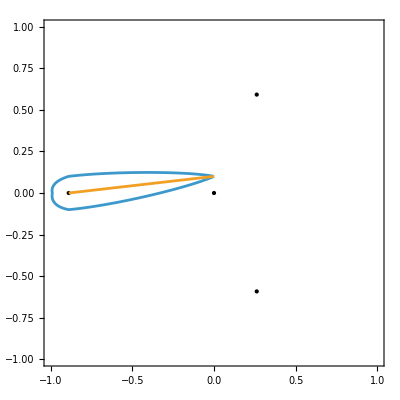

```mathematica
Show[{
Graphics[{Point[ReIm/@Join[u0, {0, -8/9}]]}],
ParametricPlot[Evaluate[ReIm/@{upath[t], upath1[t]}],{t,0,1}]
},
PlotRange->{{-1,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

```mathematica
Options[ComputeTransition2]={WorkingPrecision->60};
ComputeTransition2[el_,upath_,Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi,mon,SystMat,msg,tt=0},
Monitor[
msg="Integrating the connection...";
sol=NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA2[el,upath[t]].Psi[t],Psi[0]==IdentityMatrix[3]},Psi,{t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^7,StepMonitor:>(tt=t)];
mon=Psi[1]/. First[sol];
msg="Solving for the system matrix...";
SystMat=SystemMatrix2[F1Series2[el,upath[0],Nn,Nr],el,upath[0]];
LinearSolve[SystMat,mon.SystMat],msg<>" "<>ToString[Floor[100 tt]]<>"%."]];
```

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
mon2= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{-0.5,4.,-1.},{-1.5,9.,-2.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999999999999999159094809658, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(Ch[1,1]/.repCh).Sigma.{1,m,psi1[[1,2]],psi1[[1,3]]}
```

0.+0. ⅈ

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
mon1= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{0.,1.,-1.},{0.,0.,1.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999999999999999063544376405, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(Ch[0,0]/.repCh).Sigma.{1,m,psi1[[1,2]],psi1[[1,3]]}
```

0.+0. ⅈ

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
monB= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{-1.33333+0.119331 ⅈ,6.,-1.},{-8.66667+0.596656 ⅈ,31.,-5.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999998107022866345453149181, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Psi[.9999999999999999]/.First[a1]
```

{{1.,0.666667+0.119331 ⅈ,2.+0.715987 ⅈ},{0.,1.97471+105.748 ⅈ,-80.7197+583.323 ⅈ},{0.,-2.48934×10^16-1.89376×10^17 ⅈ,2.70898×10^16-1.06313×10^18 ⅈ}}

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[{m+1/2,1+6m}]
]
```

{0.666667+0.119331 ⅈ,2.+0.715987 ⅈ}

```mathematica
MatrixForm[monB]
```

(1. | 0. | 0.
-1.33333+0.119331 ⅈ | 6. | -1.
-8.66667+0.596656 ⅈ | 31. | -5.)

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[{-3/2+m, -19/2+5m}]
]
```

{-1.33333+0.119331 ⅈ,-8.66667+0.596656 ⅈ}

```mathematica
mB={{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}};
```

```mathematica
MatrixForm[MonodromyFromSphericalTwist[Ch[2,1]/.repCh]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-15/2 | 5 | 25 | -4)

```mathematica
Tr[monB]
```

2.

```mathematica
MatrixForm[MatrixPower[mB,3]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 2 | -1 | 0
2 | 12 | 0 | -1)

```mathematica
Chop[MatrixPower[monB,3]]
```

{{1.,0,0},{1.33333+0.238662 ⅈ,-1.,0},{4.+1.43197 ⅈ,0,-1.}}

```mathematica
MatrixForm[MonodromyFromSphericalTwist[Ch[p,q]/.repCh][[{1,3,4},{1,3,4}]]]
```

(1 | 0 | 0
-p q+q^2/2 | 1+2 p+q | -1
(2 p+q) (-p q+q^2/2) | (2 p+q)^2 | 1-2 p-q)

```mathematica
MatrixForm[mon2]
```

(1. | 0. | 0.
-0.5 | 4. | -1.
-1.5 | 9. | -2.)

```mathematica
mB
```

{{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}}

```mathematica
Dot@@(MonodromyFromSphericalTwist/@{GV[0,1,1/2],Ch[2,1]}/.repCh)//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-19/2 | 5 | 31 | -5)

```mathematica
Solve[{1+2 p+q==6, -p q+q^2/2==-3/2},{p,q}]
```

{{p→2,q→1},{p→7/4,q→3/2}}

```mathematica
MatrixForm[Inverse[MLV]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1 | 0 | 1 | 0
4 | -1 | -8 | 1)

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[4-m]
]
```

3.83333-0.119331 ⅈ

```mathematica
MatrixForm[Chop[mon1.mon2.monB]]
```

(1. | 0 | 0
-1. | 1. | 0
3.83333-0.119331 ⅈ | -8. | 1.)

### Important el values

```mathematica
PolyJ[el_,ur_, j_]=#[[1]]-j#[[2]]&@NumeratorDenominator[MirrorCurveJ[el,ur]]
```

(1-8 el ur^2-24 ur^3+16 el^2 ur^4)^3-j ur^8 (el+ur-8 el^2 ur^2-36 el ur^3-27 ur^4+16 el^3 ur^4)

```mathematica
FullSimplify[Resultant[PolyJ[el,ur,j],D[PolyJ[el,ur,j],ur], ur]]
```

-(27+256 el^3)^3 (-1728+j)^6 j^8 (4096 el^6+27 j-16 el^3 j) ((27+256 el^3) (243+256 el^3)^3-16777216 el^9 j)

```mathematica
Solve[4096 el^6+27 j-16 el^3 j==0,j]
Solve[MirrorCurveJ[el,ur]-j==0/.First[%],ur]
```

{{j→(4096 el^6)/(-27+16 el^3)}}

-(4096 el^6)/(-27+16 el^3)+((1-8 el ur^2-24 ur^3+16 el^2 ur^4)^3)/(ur^8 (el+ur-8 el^2 ur^2-36 el ur^3-27 ur^4+16 el^3 ur^4))

```mathematica
Solve[(27+256 el^3) (243+256 el^3)^3-16777216 el^9 j==0,j]
```

{{j→((27+256 el^3) (243+256 el^3)^3)/(16777216 el^9)}}

```mathematica
Simplify[Discriminant[PolyJ[el,ur,j],ur]]
```

-(27+256 el^3)^3 (387420489+4897760256 el^3+12899450880 el^6+4294967296 el^12-16777216 el^9 (-756+j)) (-1728+j)^6 j^8

```mathematica
Simplify@Solve[(387420489+4897760256 el^3+12899450880 el^6+4294967296 el^12-16777216 el^9 (-756+j))==0,j]
```

{{j→((27+256 el^3) (243+256 el^3)^3)/(16777216 el^9)}}

```mathematica
Solve[{1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4==0,D[1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4,ur]==0},{el, ur}]
```

{{el→-27/256,ur→-8/9}}

### solving PF near ur = -8/9

```mathematica
Simplify[ExpandAll[PicardFuchsQ2[el,ur]]]
```

(8+16 ur+(9-256 el) ur^2-1860 el ur^3+16 el (-189+64 el) ur^4+54 el (-27+16 el) ur^5)/(ur^2 (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))

```mathematica
Simplify[ExpandAll[PicardFuchsP2[el,z+(-8/9)]]]
```

(32 el^2 (8-9 z)^4 (4+27 z)+729 (8+18 z+243 z^2)-54 el (8-9 z)^2 (-32-144 z-1134 z^2+2187 z^3))/(z (-8+9 z) (16 el^2 (8-9 z)^4+729 (1+9 z)-27 el (8-9 z)^2 (-8-36 z+81 z^2)))

```mathematica
Simplify[Series[PicardFuchs2[(ur+8/9)^r, -27/256, ur], {ur,-8/9,1}]]
```

(8/9+ur)^r (((35 r)/36-2 r^2+r^3)/(ur+8/9)^3+((395-684 r) r)/(144 (ur+8/9)^2)+1/O[ur+8/9])

```mathematica
Solve[(35 r)/36-2 r^2+r^3==0,r]
```

{{r→0},{r→5/6},{r→7/6}}

```mathematica
(ur+8/9)+Sum[If[i==3,Nothing,a[i](ur+8/9)^i], {i,2,7}]
```

8/9+Nothing+ur+(8/9+ur)^2 a[2]+(8/9+ur)^4 a[4]+(8/9+ur)^5 a[5]+(8/9+ur)^6 a[6]+(8/9+ur)^7 a[7]

```mathematica
(ur+8/9)+Sum[If[i==3,0,a[i](ur+8/9)^i], {i,2,13}]
pi=Series[%, {ur,-8/9,13}]
```

8/9+ur+(8/9+ur)^2 a[2]+(8/9+ur)^4 a[4]+(8/9+ur)^5 a[5]+(8/9+ur)^6 a[6]+(8/9+ur)^7 a[7]+(8/9+ur)^8 a[8]+(8/9+ur)^9 a[9]+(8/9+ur)^10 a[10]+(8/9+ur)^11 a[11]+(8/9+ur)^12 a[12]+(8/9+ur)^13 a[13]

(ur+8/9)+a[2] (ur+8/9)^2+a[4] (ur+8/9)^4+a[5] (ur+8/9)^5+a[6] (ur+8/9)^6+a[7] (ur+8/9)^7+a[8] (ur+8/9)^8+a[9] (ur+8/9)^9+a[10] (ur+8/9)^10+a[11] (ur+8/9)^11+a[12] (ur+8/9)^12+a[13] (ur+8/9)^13+O[ur+8/9]^14

```mathematica
Simplify[PicardFuchs2[pi,el, ur]][[3,1;;7]];
sol=Simplify[Solve[Thread[%==0],Table[If[i==3,Nothing,a[i]],{i,2,8}]]]
```

{{a[2]→(9 (27+512 el))/(432+4096 el),a[4]→-(729 (-45927-559872 el-4423680 el^2+67108864 el^3))/(1024 (27+256 el)^3),a[5]→-(6561 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4))/(40960 (27+256 el)^4),a[6]→-(531441 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5))/(131072 (27+256 el)^5),a[7]→-1/(3670016 (27+256 el)^6)531441 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6),a[8]→-1/(33554432 (27+256 el)^7)4782969 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7)}}

```mathematica
(ur+8/9)^3+Sum[a[i](ur+8/9)^i, {i,4,14}];
pi2=Series[%, {ur,-8/9,14}]
```

(ur+8/9)^3+a[4] (ur+8/9)^4+a[5] (ur+8/9)^5+a[6] (ur+8/9)^6+a[7] (ur+8/9)^7+a[8] (ur+8/9)^8+a[9] (ur+8/9)^9+a[10] (ur+8/9)^10+a[11] (ur+8/9)^11+a[12] (ur+8/9)^12+a[13] (ur+8/9)^13+a[14] (ur+8/9)^14+O[ur+8/9]^15

```mathematica
Simplify[PicardFuchs2[pi2, el, ur]][[3,1;;7]];
sol2=Simplify@Solve[Thread[%==0],Table[a[i],{i,4,10}]]
```

{{a[4]→(27 (-99+1024 el))/(864+8192 el),a[5]→(243 (36207-211968 el+1310720 el^2))/(640 (27+256 el)^2),a[6]→(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3))/(2048 (27+256 el)^3),a[7]→(19683 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4))/(57344 (27+256 el)^4),a[8]→(177147 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5))/(524288 (27+256 el)^5),a[9]→1/(1048576 (27+256 el)^6)531441 (26338781944665-108735447541248 el+1047757897728 el^2+1146819660742656 el^3-3174865595006976 el^4-3324923162394624 el^5+31525197391593472 el^6),a[10]→1/(83886080 (27+256 el)^7)43046721 (-5066485633590165+18262870479244800 el+33734144410140672 el^2-425714076069396480 el^3+1682514386217861120 el^4-3427402044149858304 el^5-141863388262170624 el^6+11529215046068469760 el^7)}}

```mathematica
piS=Series[pi/.First[sol],{ur,-8/9,8}]
```

(ur+8/9)+(9 (27+512 el) (ur+8/9)^2)/(432+4096 el)-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) (ur+8/9)^4)/(1024 (27+256 el)^3)-(6561 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) (ur+8/9)^5)/(40960 (27+256 el)^4)-(531441 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) (ur+8/9)^6)/(131072 (27+256 el)^5)-1/(3670016 (27+256 el)^6)531441 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6) (ur+8/9)^7-1/(33554432 (27+256 el)^7)4782969 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7) (ur+8/9)^8+O[ur+8/9]^9

```mathematica
pi2S=Series[pi2/.First[sol2], {ur,-8/9, 10}]
```

(ur+8/9)^3+(27 (-99+1024 el) (ur+8/9)^4)/(864+8192 el)+(243 (36207-211968 el+1310720 el^2) (ur+8/9)^5)/(640 (27+256 el)^2)+(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3) (ur+8/9)^6)/(2048 (27+256 el)^3)+(19683 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4) (ur+8/9)^7)/(57344 (27+256 el)^4)+(177147 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5) (ur+8/9)^8)/(524288 (27+256 el)^5)+1/(1048576 (27+256 el)^6)531441 (26338781944665-108735447541248 el+1047757897728 el^2+1146819660742656 el^3-3174865595006976 el^4-3324923162394624 el^5+31525197391593472 el^6) (ur+8/9)^9+1/(83886080 (27+256 el)^7)43046721 (-5066485633590165+18262870479244800 el+33734144410140672 el^2-425714076069396480 el^3+1682514386217861120 el^4-3427402044149858304 el^5-141863388262170624 el^6+11529215046068469760 el^7) (ur+8/9)^10+O[ur+8/9]^11

```mathematica
{{1,0,0},{T0,a,b},{TD0,c,d}}.{1,pi/.{a->A},pi2/.{a->B}}
tau0=Simplify[Series[D[%[[3]],ur]/D[%[[2]],ur],{ur,-8/9,4}]]
```

{1,T0+a (ur+8/9)+a A[2] (ur+8/9)^2+b (ur+8/9)^3+(a A[4]+b B[4]) (ur+8/9)^4+(a A[5]+b B[5]) (ur+8/9)^5+(a A[6]+b B[6]) (ur+8/9)^6+(a A[7]+b B[7]) (ur+8/9)^7+(a A[8]+b B[8]) (ur+8/9)^8+(a A[9]+b B[9]) (ur+8/9)^9+(a A[10]+b B[10]) (ur+8/9)^10+(a A[11]+b B[11]) (ur+8/9)^11+(a A[12]+b B[12]) (ur+8/9)^12+(a A[13]+b B[13]) (ur+8/9)^13+O[ur+8/9]^14,TD0+c (ur+8/9)+c A[2] (ur+8/9)^2+d (ur+8/9)^3+(c A[4]+d B[4]) (ur+8/9)^4+(c A[5]+d B[5]) (ur+8/9)^5+(c A[6]+d B[6]) (ur+8/9)^6+(c A[7]+d B[7]) (ur+8/9)^7+(c A[8]+d B[8]) (ur+8/9)^8+(c A[9]+d B[9]) (ur+8/9)^9+(c A[10]+d B[10]) (ur+8/9)^10+(c A[11]+d B[11]) (ur+8/9)^11+(c A[12]+d B[12]) (ur+8/9)^12+(c A[13]+d B[13]) (ur+8/9)^13+O[ur+8/9]^14}

c/a+(3 (-b c+a d) (ur+8/9)^2)/a^2+(2 (b c-a d) (3 A[2]-2 B[4]) (ur+8/9)^3)/a^2+((-b c+a d) (-9 b+a (12 A[2]^2-8 A[2] B[4]+5 B[5])) (ur+8/9)^4)/a^3+O[ur+8/9]^5

```mathematica
Simplify[Series[J[tau0], {ur,-8/9,4}]]
```

J[c/a]+(3 (-b c+a d) J'[c/a] (ur+8/9)^2)/a^2+(2 (b c-a d) (3 A[2]-2 B[4]) J'[c/a] (ur+8/9)^3)/a^2+((b c-a d) (-2 a (-9 b+a (12 A[2]^2-8 A[2] B[4]+5 B[5])) J'[c/a]+9 (b c-a d) J''[c/a]) (ur+8/9)^4)/(2 a^4)+O[ur+8/9]^5

```mathematica
Simplify[Series[MirrorCurveJ2[el,ur], {ur,-8/9,3}]]
```

((27+256 el) (243+256 el)^3)/(16777216 el^3)-(6561 ((243+256 el)^2 (-19683-124416 el+65536 el^2)) (ur+8/9)^2)/(268435456 (el^3 (27+256 el)))-(59049 ((243+256 el)^2 (1240029+2799360 el-35979264 el^2+16777216 el^3)) (ur+8/9)^3)/(1073741824 (el^3 (27+256 el)^2))+O[ur+8/9]^4

```mathematica
Simplify[Solve[J[c/a]==((27+256 el) (243+256 el)^3)/(16777216 el^3),J[c/a]]]
```

{{J[c/a]→((27+256 el) (243+256 el)^3)/(16777216 el^3)}}

```mathematica
Simplify[Solve[-(6561 ((243+256 el)^2 (-19683-124416 el+65536 el^2)) (ur+8/9)^2)/(268435456 (el^3 (27+256 el)))==(3 (-b c+a d) J'[c/a] (ur+8/9)^2)/a^2, J'[c/a]]]
```

{{J'[c/a]→(2187 a^2 (243+256 el)^2 (-19683-124416 el+65536 el^2))/(268435456 (b c-a d) el^3 (27+256 el))}}

```mathematica
Simplify[((2187 a^2 (243+256 el)^2 (-19683-124416 el+65536 el^2))/(268435456 (b c-a d) el^3 (27+256 el)))/(((27+256 el) (243+256 el)^3)/(16777216 el^3))]
```

(2187 a^2 (-19683-124416 el+65536 el^2))/(16 (b c-a d) (27+256 el)^2 (243+256 el))

```mathematica
a1=Simplify[A[el]+B[el]piS+C1[el]pi2S]
```

A[el]+B[el] (ur+8/9)+(9 (27+512 el) B[el] (ur+8/9)^2)/(432+4096 el)+C1[el] (ur+8/9)^3+(-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) B[el])/(1024 (27+256 el)^3)+(27 (-99+1024 el) C1[el])/(864+8192 el)) (ur+8/9)^4-1/(40960 (27+256 el)^4)243 (27 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B[el]-64 (27+256 el)^2 (36207-211968 el+1310720 el^2) C1[el]) (ur+8/9)^5-1/(131072 (27+256 el)^5)729 (729 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B[el]-64 (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1[el]) (ur+8/9)^6-1/(3670016 (27+256 el)^6)19683 (27 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6) B[el]-64 (27+256 el)^2 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4) C1[el]) (ur+8/9)^7-1/(33554432 (27+256 el)^7)177147 (27 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7) B[el]-64 (27+256 el)^2 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5) C1[el]) (ur+8/9)^8+O[ur+8/9]^9

```mathematica
ClearAll[A1,A2];
A1[f_]:=-2 m u^3 D[f,{m,0},{u,1}]-m u^4 D[f,{m,0},{u,2}]+1/3 m D[f,{m,1},{u,0}]+1/3 m u D[f,{m,1},{u,1}]+1/3 m^2 D[f,{m,2},{u,0}];
A2[f_]:=1/9 u D[f,{m,0},{u,1}]+1/9 u^2 D[f,{m,0},{u,2}]+4/9 m D[f,{m,1},{u,0}]-4/9 m u D[f,{m,1},{u,1}]-u^2 D[f,{m,1},{u,1}]+4/9 m^2 D[f,{m,2},{u,0}];
```

```mathematica
Simplify[A1[f[m^3, u/m]]/.{m->el^(1/3), u->ur el^(1/3)}]
```

el (-2 ur^3 f^(0,1)[el,ur]-ur^4 f^(0,2)[el,ur]+3 f^(1,0)[el,ur]-ur f^(1,1)[el,ur]+3 el f^(2,0)[el,ur])

```mathematica
Simplify[A2[f[m^3, u/m]]/.{m->el^(1/3), u->ur el^(1/3)}]
```

ur (1+ur) f^(0,1)[el,ur]+ur^2 (1+ur) f^(0,2)[el,ur]+el (4 f^(1,0)[el,ur]-ur (4+3 ur) f^(1,1)[el,ur]+4 el f^(2,0)[el,ur])

```mathematica
ClearAll[PF1,PF2];
PF1[f_,el_,ur_]:=(-2 ur^3 D[f,ur]-ur^4 D[f,{ur,2}]+3 D[f,el]-ur D[f,el,ur]+3 el D[f,{el,2}]);
PF2[f_,el_,ur_]:=ur (1+ur) D[f,ur]+ur^2 (1+ur) D[f,{ur,2}]+el (4 D[f,el]-ur (4+3 ur) D[f,ur,el]+4 el D[f,{el,2}]);
```

```mathematica
eqns={
512 B[el]+3 (27+256 el) (27 A'[el]+8 B'[el]+27 el A''[el])==0,
20736 (729+3456 el+32768 el^2) B[el]+(27+256 el) (-8192 (27+256 el) C1[el]+2187 ((81+1024 el) B'[el]+3 el (27+256 el) B''[el]))==0,
20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el])==0
}
```

```mathematica
(6 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)^4+1/(864 (27+256 el)^3)(-4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el]+81 (-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el])))
```

```mathematica
temp=Simplify[First@Solve[20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el])==0,C1'[el]]]
Simplify[D[C1'[el]/.temp,el]]
Simplify[81 ((64 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el]))==4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el]/.{C1''[el]->%}]
```

{C1'[el]→(20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]))/(192 (27+256 el)^3)}

-(6912 (-8019+124416 el+1441792 el^2) B[el])/(27+256 el)^4+1/(192 (27+256 el)^3)(23068672 (27+256 el) C1[el]+10368 (243+183168 el+720896 el^2) B'[el]+(27+256 el) (-90112 (27+256 el) C1'[el]+243 (243+1152 el+65536 el^2) B''[el]))

(10368 (6436341+255301632 el+386187264 el^2-11324620800 el^3+4294967296 el^4) B[el])/(27+256 el)+27 (27+256 el) (64 (-8019-31104 el+425984 el^2) C1'[el]+243 el (243+1152 el+65536 el^2) B''[el])==8192 (754515+2301696 el-44236800 el^2+16777216 el^3) C1[el]+4374 (-45927-575424 el-16146432 el^2+20971520 el^3) B'[el]

```mathematica
temp1
```

{(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0,81 ((256 (729+3456 el+32768 el^2) B[el])/(27+256 el)+27 (81+1024 el) B'[el]+81 el (27+256 el) B''[el])==8192 (27+256 el) C1[el],81 ((256 (-45927-2426112 el-16809984 el^2+16777216 el^3) B[el])/(27+256 el)+27 (729+62208 el+131072 el^2) B'[el]+(27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el]))==8192 (-15309-131328 el+131072 el^2) C1[el],81 ((64 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el]))==4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el],(5184 (4570924041+211472892288 el+1772922028032 el^2+2605115768832 el^3+5798205849600 el^4-4398046511104 el^5) B[el])/(27+256 el)+4096 (-565276077-5974394112 el-8408530944 el^2-22649241600 el^3+17179869184 el^4) C1[el]+4374 (13286025+204493248 el+2884460544 el^2+7587495936 el^3+98784247808 el^4) B'[el]==243 (27+256 el) (96 (225261+1810944 el+3997696 el^2+67108864 el^3) C1'[el]-27 el (-45927-559872 el-4423680 el^2+67108864 el^3) B''[el]+32 el (27+256 el)^2 (-99+1024 el) C1''[el]),8192 (247781709045+2646173702016 el-1299512180736 el^2-39740246065152 el^3-5798205849600 el^4+10995116277760 el^5) C1[el]+2187 (-24063117039-404904189312 el-4886204497920 el^2+3864866586624 el^3+99265284145152 el^4+483785116221440 el^5) B'[el]==1/(27+256 el)20736 (1007766785331+47186450819712 el+353710199070720 el^2-531374819770368 el^3-5266785787969536 el^4-742170348748800 el^5+1407374883553280 el^6) B[el]+81 (27+256 el) (64 (-888037911-7553233152 el+11816534016 el^2+106602430464 el^3+687194767360 el^4) C1'[el]-81 el (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B''[el]+192 el (27+256 el)^2 (36207-211968 el+1310720 el^2) C1''[el]),8192 (-18176348802087-205517979202176 el+51671007903744 el^2+2275559451131904 el^3-11256578854354944 el^4+1009351674298368 el^5+1125899906842624 el^6) C1[el]+2187 (1758243319245+31202610224256 el+401436393652224 el^2+274885578326016 el^3-4475809041481728 el^4+27311868833955840 el^5+79938893385826304 el^6) B'[el]==1/(27+256 el)20736 (-73872176581053-3548649541343616 el-27829452534718464 el^2+26985568684474368 el^3+197681174619881472 el^4-1461682236750299136 el^5+129197014310191104 el^6+144115188075855872 el^7) B[el]+81 (27+256 el) (64 (65148820749+628500549888 el-531672367104 el^2-4046287011840 el^3+30227979829248 el^4+109951162777600 el^5) C1'[el]-729 el (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B''[el]+64 el (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1''[el])}

```mathematica
20736 (-45927-2426112 el-16809984 el^2+16777216 el^3) B[el]+(27+256 el) (-8192 (-15309-131328 el+131072 el^2) C1[el]+81 (27 (729+62208 el+131072 el^2) B'[el]+(27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el])))/.temp//Simplify
```

-54 (20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el]))

```mathematica
Simplify[PF1[a1,el,ur]][[3]];
temp1=Simplify[Thread[%==0]];
```

gpt

```mathematica
gpteqns={
el (256 el+27)^2 B''[el]+(256 el+27) (512 el+27) B'[el]+(16384 el+1920) B[el]==0,
C1[el]==(81/(64 (256 el+27)^2))*((65536 el^2-3456 el+243) B[el]-(27648 el^2+2916 el) B'[el]),
(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0
}
```

{(1920+16384 el) B[el]+(27+256 el) (27+512 el) B'[el]+el (27+256 el)^2 B''[el]==0,C1[el]==(81 ((243-3456 el+65536 el^2) B[el]-(2916 el+27648 el^2) B'[el]))/(64 (27+256 el)^2),(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0}

```mathematica
B[el]/.DSolve[el (256 el+27)^2 B''[el]+(256 el+27) (512 el+27) B'[el]+(16384 el+1920) B[el]==0, B[el],el]
```

{[el]}

```mathematica
z[el_]:=-(256 el)/27;

F0[z_]:=Hypergeometric2F1[1/3,1/3,1,z];

F1[z_]:=F0[z] Log[z]+Sum[(Pochhammer[1/3,n]^2/Factorial[n]^2)*(2 PolyGamma[n+1]-2 PolyGamma[n+1/3])*z^n,{n,1,Infinity}];

Bsol[el_]:=(1-z[el])^(-1/6) (C[1] F0[z[el]]+C[2] F1[z[el]]);
```

```mathematica
bsol=Simplify[Bsol[el]]
```

1/(1+(256 el)/27)^(1/6)(C[1] Hypergeometric2F1[1/3,1/3,1,-(256 el)/27]-1/3 C[2] (√3 π+6 EulerGamma Hypergeometric2F1[1/3,1/3,1,-(256 el)/27]+9 Log[3]-3 Hypergeometric2F1[1/3,1/3,1,-(256 el)/27] Log[-(256 el)/27]-6 Gamma[1/3] HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1/3,1/3,1/3},{1,1/3},-(256 el)/27]+6 Hypergeometric2F1^(0,0,1,0)[1/3,1/3,1,-(256 el)/27]))

```mathematica
Coefficient[gpteqns[[1,1]], {B''[el], B'[el], B[el]}]
Factor[{%[[2]],%[[3]]}/%[[1]]]
```

{el (27+256 el)^2,(27+256 el) (27+512 el),1920+16384 el}

{(27+512 el)/(el (27+256 el)),(128 (15+128 el))/(el (27+256 el)^2)}

```mathematica
Simplify[Series[gpteqns[[1,1]]/.{B->Function[el,Evaluate[1+a[1]el+a[2]el^2+a[3]el^3+a[4]el^4+a[5]el^5+a[6]el^6]]}, {el,0,10}]]
Simplify[Solve[%[[3,1;;6]]==0,Array[a,6]]]
Simplify[Table[a[i]^(1/i),{i,1,6}]/.First[%]]
```

(1920+729 a[1])+4 (4096+5664 a[1]+729 a[2]) el+(147456 a[1]+71040 a[2]+6561 a[3]) el^2+16 (25600 a[2]+9192 a[3]+729 a[4]) el^3+(802816 a[3]+250752 a[4]+18225 a[5]) el^4+12 (110592 a[4]+31840 a[5]+2187 a[6]) el^5+128 (15488 a[5]+4227 a[6]) el^6+2768896 a[6] el^7+O[el]^11

{{a[1]→-640/243,a[2]→876544/59049,a[3]→-13112442880/129140163,a[4]→23818110238720/31381059609,a[5]→-45525429271920640/7625597484987,a[6]→809445203270466273280/16677181699666569}}

{-640/243,(64 √214)/243,64/243 (-12505)^(1/3) (2/3)^(2/3),(64 1419670^(1/4))/(243 √3),64/243 (-10599715)^(1/5) (2/3)^(2/5),(64 2^(1/3) 2944744495^(1/6))/(243 3^(2/3))}

```mathematica
Assuming[n∈Integers,Simplify[SeriesCoefficient[(128 (15+128 el))/(el (27+256 el)^2),{el,0,n}]]]
```

Piecewise[{{-(-1)^n 3^(-8-3 n) 4^(7+4 n) (11+n), n>-2}, {0, True}}]

```mathematica
Assuming[n∈Integers,Simplify[SeriesCoefficient[(27+512 el)/(el (27+256 el)),{el,0,n}]]]
```

Piecewise[{{1, n==-1}, {(256/27)^(1+n) ⅇ^(ⅈ n π), n≥0}, {0, True}}]

```mathematica
Limit[(256/27)^(1+n) ⅇ^(ⅈ n π),n->-1]
```

-1

```mathematica
Simplify[Series[Normal[piS]/.{ur->-8/9+z}, {z,0,4}]]
```

z+(9 (27+512 el) z^2)/(432+4096 el)-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) z^4)/(1024 (27+256 el)^3)+O[z]^5

```mathematica
Simplify[Series[Normal[pi2S]/.{ur->-8/9+z}, {z,0,6}]]
```

z^3+(27 (-99+1024 el) z^4)/(864+8192 el)+(243 (36207-211968 el+1310720 el^2) z^5)/(640 (27+256 el)^2)+(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3) z^6)/(2048 (27+256 el)^3)+O[z]^7

```mathematica
PF1[ϖ[el, ur],el,ur]
```

-2 ur^3 ϖ^(0,1)[el,ur]-ur^4 ϖ^(0,2)[el,ur]+3 ϖ^(1,0)[el,ur]-ur ϖ^(1,1)[el,ur]+3 el ϖ^(2,0)[el,ur]

```mathematica
PF2[ϖ[el, ur],el,ur]
```

ur (1+ur) ϖ^(0,1)[el,ur]+ur^2 (1+ur) ϖ^(0,2)[el,ur]+el (4 ϖ^(1,0)[el,ur]-ur (4+3 ur) ϖ^(1,1)[el,ur]+4 el ϖ^(2,0)[el,ur])

```mathematica
ϖ
```

ϖ

```mathematica
a2=Simplify[PF1[a1,el,ur]];
a3=Simplify[PF2[a1,el,ur]];
```

```mathematica
Simplify[Thread[a3[[3]]==0]]
```

{(512 el B[el])/(27+256 el)+3 el (27 A'[el]+8 B'[el]+27 el A''[el])==0,(81 (-243+14976 el+32768 el^2) B[el])/(27+256 el)+64 (27+256 el) C1[el]+486 el ((45+512 el) B'[el]+el (27+256 el) B''[el])==0,el (-(165888 (243+11088 el+81920 el^2) B[el])/(27+256 el)+188416 (27+256 el) C1[el]+243 (243+29952 el+131072 el^2) B'[el]+3 (27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el]))==0,el (-(648 (-247131-2519424 el+122093568 el^2+1140850688 el^3) B[el])/(27+256 el)+512 (-27459+230400 el+4653056 el^2) C1[el]-243 (-2187+15552 el+368640 el^2+8388608 el^3) B'[el]+24 (27+256 el)^2 (3 (-15+512 el) C1'[el]+el (27+256 el) C1''[el]))==0,el ((5184 (107882523+4619783808 el+40931868672 el^2+203541184512 el^3+1228360646656 el^4) B[el])/(27+256 el)-4096 (13377879+121616640 el+467140608 el^2+4898947072 el^3) C1[el]+486 (2775303+32332608 el+611131392 el^2+3435134976 el^3+55834574848 el^4) B'[el]-9 (27+256 el) (32 (430839+2280960 el+18284544 el^2+335544320 el^3) C1'[el]-27 el (-45927-559872 el-4423680 el^2+67108864 el^3) B''[el]+32 el (27+256 el)^2 (-99+1024 el) C1''[el]))==0,el ((20736 (-24601998213-1080052504416 el-7080320471040 el^2+19467787567104 el^3+185619896598528 el^4+673450872012800 el^5) B[el])/(27+256 el)-8192 (-6046912845-55106941248 el+73331785728 el^2+1056813613056 el^3+5325759447040 el^4) C1[el]+243 (-5294746683-75937958784 el-749780582400 el^2+4274591367168 el^3+23811298689024 el^4+285873023221760 el^5) B'[el]-3 (27+256 el) (64 (-585116541-3387785472 el+14842331136 el^2+73383542784 el^3+1202590842880 el^4) C1'[el]-81 el (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B''[el]+192 el (27+256 el)^2 (36207-211968 el+1310720 el^2) C1''[el]))==0,el (1/(27+256 el)20736 (1858542179175+84987636573312 el+588716587524096 el^2-1125084372664320 el^3-3466573331300352 el^4+44886462692327424 el^5+105271641289785344 el^6) B[el]-8192 (457314014997+4552490832768 el-5177087115264 el^2-47600438870016 el^3+286044821913600 el^4+829031767343104 el^5) C1[el]+243 (398053029087+6226345749888 el+67955274694656 el^2-107204183064576 el^3-38094212431872 el^4+6254022138789888 el^5+48413695994232832 el^6) B'[el]-3 (27+256 el) (576 (4917423573+36637463808 el-98824126464 el^2-56396611584 el^3+2156073582592 el^4+21990232555520 el^5) C1'[el]-729 el (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B''[el]+64 el (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1''[el]))==0}

```mathematica
gpteqns[[2]]
```

C1[el]==(81 ((243-3456 el+65536 el^2) B[el]-(2916 el+27648 el^2) B'[el]))/(64 (27+256 el)^2)

```mathematica
Series[a1, {ur,-8/9,3}]
```

A[el]+B[el] (ur+8/9)+(9 (27+512 el) B[el] (ur+8/9)^2)/(432+4096 el)+C1[el] (ur+8/9)^3+O[ur+8/9]^4

```mathematica
URoot[1,2]
```

```mathematica
b0=Simplify[NodalCurvebFrommu[1, URoot[1,2]]]
```

(1-2 √(1+12 ^2)+√(3+36 ^2-6 √(1+12 ^2)))/(1+√(1+12 ^2))

```mathematica
N[b0, 50]
```

-0.7251497610490148665275651524636838940601276942613+0.68859118789783872858051959055806444225530679847176 ⅈ

```mathematica
KerrDoranP[N[b0,100]]/.LiEval
```

1.1573221007466653124323507573331906248339156872543503424470593855824166969397791401809354208310299

```mathematica
KerrDoranQ[N[b0,100]]/.LiEval
```

0.5235987755982988730771072305465838140328615665625176368291574320513027343810348331046724708903528+1.1573221007466653124323507573331906248339156872543503424470593855824166969397791401809354208310299 ⅈ

```mathematica
Pi/6//N
```

0.523599

```mathematica
FullSimplify[KerrDoranQ[b], Im[b]>0]
```

1/(6 π)(-3 Li2[1/b^3]+9 Li2[1/b^2]-6 Li2[1/b]+9 Li2[b]-3 Li2[b^2]-3 Log[1/b^2] Log[(-1+b)/b]+6 Log[1-1/b^2] (Log[1/b^2]-Log[b])+9 Log[1-b] Log[b]+3 Log[1-1/b^3] (-Log[1/b^2]+Log[b])+Log[1/b^2] Log[2+1/b+b]+2 Log[b] Log[2+1/b+b]-6 Log[b] Log[1-b^2])

```mathematica
KerrDoranQ1[b_] := 1/2/Pi(Li2[b^3]-4Li2[b^2]+5Li2[b])+1/4/Pi Log[b](6Log[b^2+b+1]+Log[b]-16Log[b+1]-4Pi I);
```

```mathematica
KerrDoranQ1[N[b0,100]]/.LiEval
```

6.04723961442988767308143479331193359143398292162099171115878521608793637552810859100131441602919916+1.1573221007466653124323507573331906248339156872543503424470593855824166969397791401809354208310299 ⅈ

```mathematica
a1=Simplify[D[KerrDoranQ1[b]-KerrDoranQ[b],b]];
```

```mathematica
a1p=FullSimplify[a1/.{Li2'[b_]:>-Log[1-b]/b}]
```

-((6 ⅈ (1+b) (1+b+b^2) π+15 (1+b) (1+b+b^2) Log[1-b]+(-1+b)^3 Log[1/b^2]-2 Log[b]+2 b (3+(-3+b) b) Log[b]+24 Log[1+b]-24 Log[1-b^2]-9 Log[1+b+b^2]+9 Log[1-b^3]+3 b (2+b (2+b)) (8 Log[1+b]-8 Log[1-b^2]-3 Log[1+b+b^2]+3 Log[1-b^3]))/(6 b (1+b) (1+b+b^2) π))

```mathematica
a2=Simplify[D[b a1,b]];
```

```mathematica
Simplify[a2/.{Li2->Function[b, PolyLog[2,b]]}]
```

-((-1+b)^2 (5+8 b+5 b^2) (Log[1/b^2]+2 Log[b]))/(6 (1+b)^2 (1+b+b^2)^2 π)

```mathematica
a1/.{Li2->Function[b, PolyLog[2,b]]}
```

1/(6 π)(-(6 ⅈ π)/b+(6 Log[1-1/b])/b-(15 Log[1-b])/b+(3 Log[1/b^2])/((-1+b) b)+Log[1/b^2]/(b (1+b)^2)-(b Log[1/b^2])/(1+b)^2+(12 Log[1/b^2])/(b-b^3)-(9 Log[1/b^2])/(b-b^4)+(3 Log[1/b])/(-1+b)+(3 Log[1/b])/((-1+b) b)-(3 Log[1/b])/(b (1+b)^2)+(3 b Log[1/b])/(1+b)^2-(6 b Log[1/b])/(-1+b^2)+(6 Log[1/b])/(b-b^3)-(6 Log[(-1+b)/b])/b-(6 Log[b])/(-1+b)+(3 Log[b])/b+(3 Log[b])/((-1+b) b)-Log[b]/(b (1+b)^2)+(b Log[b])/(1+b)^2-(24 Log[b])/(1+b)+(6 b Log[b])/(-1+b^2)+(9 Log[b])/(1+b+b^2)+(18 b Log[b])/(1+b+b^2)-(6 Log[b])/(b-b^3)+(9 Log[b])/(b-b^4)-(24 Log[1+b])/b+(24 Log[1-b^2])/b+(9 Log[1+b+b^2])/b-(9 Log[1-b^3])/b)

```mathematica
Plot3D[Im[Log[1/b^2]+2 Log[b]/.{b->b1+I b2}], {b1,-4,4},{b2,-4,4}]
```

-Graphics3D-

```mathematica
Plot3D[Im[a1p/.{b->b1+I b2}], {b1,-4,4},{b2,-4,4}]
```

-Graphics3D-

```mathematica
Simplify[1-Euler[{r,dF,dB,ch2},{r,dF,dB,ch2}]]
```

1-dB^2+2 dB dF-2 ch2 r-r^2

```mathematica
mb=Dot@@MonodromyFromSphericalTwist/@{GV[0,1,1/2], Ch[2,1]}/.repCh
```

{{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}}

```mathematica
MatrixForm[mb]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-19/2 | 5 | 31 | -5)

```mathematica
Solve[MonodromyOnTau[mb,tau]==tau,tau]//N
```

{{tau→5.5-0.866025 ⅈ},{tau→5.5+0.866025 ⅈ}}

```mathematica
Solve[-1/(tau+1)==tau,tau]
```

{{tau→-(-1)^(1/3)},{tau→(-1)^(2/3)}}

```mathematica
N[Exp[I Pi/3]]
```

0.5+0.866025 ⅈ

```mathematica
N[-1/(Exp[I Pi/3]-1)]
```

0.5+0.866025 ⅈ

## Kerr-Doranology

```mathematica
MirrorCurveDelta2[el,ur]
```

1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4

```mathematica
a1=MirrorCurve2[x,y,el,ur]
```

-1/ur+x+y+(el (1+y))/(x y)

```mathematica
s1=Solve[a1==0,y]
```

{{y→(-el ur+x-ur x^2-√(-4 el ur^2 x+(el ur-x+ur x^2)^2))/(2 ur x)},{y→(-el ur+x-ur x^2+√(-4 el ur^2 x+(el ur-x+ur x^2)^2))/(2 ur x)}}

```mathematica
m1={Y->el+x (-1/ur+x+2 y), X->x};
```

```mathematica
Simplify[Y^2-(-4 el X+(el-X/ur+X^2)^2)/.m1/.s1]
```

{0,0}

```mathematica
m1Inv=First[Simplify@Solve[Thread[{X,Y}==({X,Y}/.m1)],{x,y}]]
```

{x→X,y→(-el ur+X-ur X^2+ur Y)/(2 ur X)}

```mathematica
f4[X_,el_,ur_]:=-4 el X+(el-X/ur+X^2)^2;
```

```mathematica
Expand[f4[X,el,ur]]
```

el^2-4 el X-(2 el X)/ur+2 el X^2+X^2/ur^2-(2 X^3)/ur+X^4

```mathematica
m2={x->1/2/ur+(b Y-a/2)/(X+c), y->a/(X+c)};
```

```mathematica
a2=Simplify[Y^2/.First@Solve[a1==0/.m2,Y]]
```

-(-a^3 ur^2+2 a^2 ur (c+X)+a (-1+4 el ur^2) (c+X)^2+4 el ur^2 (c+X)^3)/(4 a b^2 ur^2)

```mathematica
sol={a->-el/(4 b^2), c->(-1+4 el ur^2)/(48 b^2 ur^2)};
```

```mathematica
a3=Simplify[a2/.sol/.{b->1/12/ur}];
Series[a3,{X,0,4}]
```

4 (54-3456 el^3 ur^6-648 el ur^2 (1+3 ur)+432 el^2 ur^4 (6+18 ur+27 ur^2))+4 (-27-432 el^2 ur^4+216 el ur^2 (1+3 ur)) X+4 X^3+O[X]^5

```mathematica
Simplify[sol/.{b->1/12/ur}]
```

{a→-36 el ur^2,c→-3+12 el ur^2}

```mathematica
g2=Simplify[-Coefficient[a3,X]]
```

108 (1+16 el^2 ur^4-8 el ur^2 (1+3 ur))

```mathematica
g3=Simplify[-a3/.{X->0}]
```

-216 (1-64 el^3 ur^6-12 el ur^2 (1+3 ur)+24 el^2 ur^4 (2+6 ur+9 ur^2))

```mathematica
disDelta=Simplify[g2^3-27g3^2]
```

2176782336 el^3 ur^8 (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)

```mathematica
J=Simplify[1728g2^3/disDelta]
```

((1+16 el^2 ur^4-8 el ur^2 (1+3 ur))^3)/(el^3 ur^8 (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))

```mathematica
a1=Expand[4(X-X0)^2(X-X1)]
```

4 X^3-8 X^2 X0+4 X X0^2-4 X^2 X1+8 X X0 X1-4 X0^2 X1

```mathematica
Coefficient[a1,X^2]
```

-8 X0-4 X1

```mathematica
a2=a1/.{X1->-2X0}
{g2p,g3p}={-Coefficient[a2,X],-(a2/.X->0)}
```

4 X^3-12 X X0^2+8 X0^3

{12 X0^2,-8 X0^3}

```mathematica
g3p/g2p
```

-(2 X0)/3

```mathematica
del = MirrorCurveDelta2[el,ur]
```

1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4

```mathematica
X0v=Simplify[-(3 g3)/(2 g2)]
```

(3 (1-64 el^3 ur^6-12 el ur^2 (1+3 ur)+24 el^2 ur^4 (2+6 ur+9 ur^2)))/(1+16 el^2 ur^4-8 el ur^2 (1+3 ur))

```mathematica
a5=FullSimplify[X0v/.ur->Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]]
```

(3+12 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2 (-3+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (-9+2 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (6+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (18+(27-8 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1])))))/(1+8 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2 (-1+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (-3+2 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1])))

```mathematica
Factor[a5/.Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]->ur]
```

-(3 (-1+12 el ur^2+36 el ur^3-48 el^2 ur^4-144 el^2 ur^5-216 el^2 ur^6+64 el^3 ur^6))/(1-8 el ur^2-24 el ur^3+16 el^2 ur^4)

```mathematica
s4=Simplify[{X->t^2-2X0, Y->2(t^3-3 t X0)}]
```

{X→t^2-2 X0,Y→2 (t^3-3 t X0)}

```mathematica
Simplify[Y^2-a2/.s4]
```

0

```mathematica
a7=Simplify@Together[{x,y}/.m2/.sol/.{b->1/12/ur}/.s4]
```

{(-9+3 t^2+t^3+36 el ur^2 (1+3 ur)-6 X0-3 t X0)/(6 ur (-3+t^2+12 el ur^2-2 X0)),-(36 el ur^2)/(-3+t^2+12 el ur^2-2 X0)}

```mathematica
s5=Solve[(-3+t^2+12 el ur^2-2 X0)==t^2-t1^2,t1]
```

{{t1→-√(3-12 el ur^2+2 X0)},{t1→√(3-12 el ur^2+2 X0)}}

```mathematica
s6=Solve[(-3+t^2+12 el ur^2-2 X0)==t^2-t1^2,X0]
```

{{X0→1/2 (-3+t1^2+12 el ur^2)}}

```mathematica
a8=Simplify[a7/.First[s6]]
```

{(9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 el t ur^2+216 el ur^3)/(12 t^2 ur-12 t1^2 ur),-(36 el ur^2)/(t^2-t1^2)}

```mathematica
Factor[a8]
```

{(9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 el t ur^2+216 el ur^3)/(12 (t-t1) (t+t1) ur),-(36 el ur^2)/((t-t1) (t+t1))}

```mathematica
a9=NumeratorDenominator[a8[[1]]]
```

{9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 el t ur^2+216 el ur^3,12 t^2 ur-12 t1^2 ur}

```mathematica
Simplify[t1^2/.First[s5]/.{X0->X0v}]
s8=Simplify[Solve[{1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4==0,t1^2==%}, {el, ur}]]
s8=s8[[2]]
```

-(9 (-1+64 el^3 ur^6+4 el ur^2 (3+8 ur)-16 el^2 ur^4 (3+8 ur+9 ur^2)))/(1+16 el^2 ur^4-8 el ur^2 (1+3 ur))

{{el→(27 (-3+t1) (-1+t1)^3)/(16 t1^4),ur→(2 t1^2)/(9-9 t1)},{el→(27 (1+t1)^3 (3+t1))/(16 t1^4),ur→(2 t1^2)/(9 (1+t1))}}

{el→(27 (1+t1)^3 (3+t1))/(16 t1^4),ur→(2 t1^2)/(9 (1+t1))}

```mathematica
Simplify[a8]
```

```mathematica
{(f ur^3)/(12 t^2 ur-12 t1^2 ur),-(36 el ur^2)/(t^2-t1^2)}
```

```mathematica
a9[[1]]
```

9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 el t ur^2+216 el ur^3

```mathematica
a10=Simplify[a9[[1]]/.s8]
```

2 (t-t1)^2 (3+t+2 t1)

```mathematica
a11=Simplify[a8/.{a9[[1]]->a10}]
```

{((t-t1) (3+t+2 t1))/(6 (t+t1) ur),-(36 el ur^2)/(t^2-t1^2)}

```mathematica
Solve[el==1/.s8,t1]
N[ur/.s8/.%]
```

{{t1→},{t1→},{t1→},{t1→}}

{-3.02572,0.263185,-0.255099+0.221553 ⅈ,-0.255099-0.221553 ⅈ}

```mathematica
X0v2=Simplify[X0/.First[s6]/.s8]
```

t1 (2+t1)

```mathematica
s9=First@Solve[z==(t-Sqrt[3X0])/(t+Sqrt[3X0]), t]
```

{t→(-√3 √X0-√3 √X0 z)/(-1+z)}

```mathematica
Factor[a11/.s8]
a12=Factor[Simplify[%/.s9]]
```

{(3 (t-t1) (1+t1) (3+t+2 t1))/(4 t1^2 (t+t1)),(3 (1+t1) (3+t1))/((-t+t1) (t+t1))}

{-(3 (1+t1) (-3-2 t1-√3 √X0+3 z+2 t1 z-√3 √X0 z) (-t1+√3 √X0+t1 z+√3 √X0 z))/(4 t1^2 (-1+z) (-t1-√3 √X0+t1 z-√3 √X0 z)),(3 (1+t1) (3+t1) (-1+z)^2)/(t1^2-3 X0-2 t1^2 z-6 X0 z+t1^2 z^2-3 X0 z^2)}

```mathematica
a15=RationalData[a12[[1]],z]
```

{{1,1,-1,-1},{(3+2 t1+√3 √X0)/(3+2 t1-√3 √X0),(t1-√3 √X0)/(t1+√3 √X0),1,(t1+√3 √X0)/(t1-√3 √X0)}}

```mathematica
Solve[t1^2-3 X0-2 t1^2 z-6 X0 z+t1^2 z^2-3 X0 z^2==0,z]
```

{{z→(t1^2-2 √3 t1 √X0+3 X0)/(t1^2-3 X0)},{z→(t1^2+2 √3 t1 √X0+3 X0)/(t1^2-3 X0)}}

```mathematica
FullSimplify[a12[[2]]]
Factor[t1^2 (-1+z)^2-3 X0 (1+z)^2,Extension->Automatic]
```

(3 (1+t1) (3+t1) (-1+z)^2)/(t1^2 (-1+z)^2-3 X0 (1+z)^2)

t1^2-3 X0-2 t1^2 z-6 X0 z+t1^2 z^2-3 X0 z^2

```mathematica
a13=Coefficient[t1^2 (-1+z)^2-3 X0 (1+z)^2,z^2]
```

t1^2-3 X0

```mathematica
z/.Solve[t1^2 (-1+z)^2-3 X0 (1+z)^2==0,z]
a14=a13(z-%[[1]])(z-%[[2]])
```

{(t1^2-2 √3 t1 √X0+3 X0)/(t1^2-3 X0),(t1^2+2 √3 t1 √X0+3 X0)/(t1^2-3 X0)}

(t1^2-3 X0) (-(t1^2-2 √3 t1 √X0+3 X0)/(t1^2-3 X0)+z) (-(t1^2+2 √3 t1 √X0+3 X0)/(t1^2-3 X0)+z)

```mathematica
a16=RationalData[Numerator[a12[[2]]]/a14,z]
```

{{2,-1,-1},{1,(t1^2+2 √3 t1 √X0+3 X0)/(t1^2-3 X0),(t1^2-2 √3 t1 √X0+3 X0)/(t1^2-3 X0)}}

```mathematica
a17={{2,-1,-1},{1,(t1+√3 √X0)/(t1-√3 √X0),(t1-√3 √X0)/(t1+√3 √X0)}};
```

```mathematica
a15
```

{{1,1,-1,-1},{(3+2 t1+√3 √X0)/(3+2 t1-√3 √X0),(t1-√3 √X0)/(t1+√3 √X0),1,(t1+√3 √X0)/(t1-√3 √X0)}}

```mathematica
(t1-√3 √X0)/(t1+√3 √X0)/.{X0->X0v2}
```

(t1-√3 √(t1 (2+t1)))/(t1+√3 √(t1 (2+t1)))

```mathematica
Solve[(t1-√3 h)/(t1+√3 h)==b,h]
```

{{h→(t1-b t1)/(√3+√3 b)}}

```mathematica
Simplify[Solve[((t1-b t1)/(√3+√3 b))^2-X0v2==0,t1]]
s11=Last[%]
```

{{t1→0},{t1→-(3 (1+b)^2)/(1+4 b+b^2)}}

{t1→-(3 (1+b)^2)/(1+4 b+b^2)}

```mathematica
(*{t1->-\frac{3 (b+1)^2}{b^2+4 b+1}}*)
```

```mathematica
a20=Simplify[a15/.{X0->X0v2}/.s11,1<b<Infinity]
```

{{1,1,-1,-1},{1/b^2,b,1,1/b}}

```mathematica
a21=Simplify[a16/.{X0->X0v2}/.s11,1<b<Infinity]
```

{{2,-1,-1},{1,1/b,b}}

```mathematica
Simplify[s8/.s11]
```

{el→-(b (1+b+b^2)^3)/(1+b)^8,ur→-(1+b)^4/((1+b+b^2) (1+4 b+b^2))}

```mathematica
temp=N@Solve[-(b (1+b+b^2)^3)/(1+b)^8==1,b]
N@Simplify[ur/.s8/.s11]/.%
```

{{b→-4.40252},{b→-0.227143},{b→-1.01658-1.12208 ⅈ},{b→-1.01658+1.12208 ⅈ},{b→-0.72515-0.688591 ⅈ},{b→-0.72515+0.688591 ⅈ},{b→-0.443438-0.489456 ⅈ},{b→-0.443438+0.489456 ⅈ}}

{-3.02572,-3.02572,-0.255099-0.221553 ⅈ,-0.255099+0.221553 ⅈ,0.263185+9.36751×10^-17 ⅈ,0.263185-9.36751×10^-17 ⅈ,-0.255099+0.221553 ⅈ,-0.255099-0.221553 ⅈ}

```mathematica
temp=Solve[1==el/.s8,t1]
```

{{t1→},{t1→},{t1→},{t1→}}

```mathematica
N[(t1-√3 √X0)/(t1+√3 √X0)/.{X0->X0v2}/.temp]
```

{-4.40252,-0.72515+0.688591 ⅈ,-0.443438-0.489456 ⅈ,-0.443438+0.489456 ⅈ}

```mathematica
b/.temp
```

{b,b,b,b}

```mathematica
1/b/.temp
```

{1/b,1/b,1/b,1/b}

```mathematica
Product[a20[[2,i]]^a20[[1,i]], {i,4}]
```

1

```mathematica
Product[a21[[2,i]]^-a21[[1,i]], {i,3}]
```

1

```mathematica
Simplify@Expand[Limit[a12,z->0]/.{X0->X0v2}]
```

{(3 (3+4 t1+t1^2))/(4 t1^2),-(3 (1+t1))/(2 t1)}

```mathematica
Simplify[Limit[a12,z->Infinity]/.{X0->X0v2}]
{Ab,Bb}=Simplify[%/.s11]
```

{(3 (3+4 t1+t1^2))/(4 t1^2),-(3 (1+t1))/(2 t1)}

{-(b (1+b+b^2))/(1+b)^4,-(1+b+b^2)/(1+b)^2}

```mathematica
s12=Simplify[s8/.s11]
```

{el→-(b (1+b+b^2)^3)/(1+b)^8,ur→-(1+b)^4/((1+b+b^2) (1+4 b+b^2))}

```mathematica
s12/.{b->1}
```

{el→-27/256,ur→-8/9}

```mathematica
s8
```

{el→(27 (1+t1)^3 (3+t1))/(16 t1^4),ur→(2 t1^2)/(9 (1+t1))}

```mathematica
Simplify[Solve[t1==-(3 (1+b)^2)/(1+4 b+b^2),b]]
```

{{b→-(3+2 t1+√3 √(t1 (2+t1)))/(3+t1)},{b→(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)}}

Kerr Doran formula

```mathematica
KerrDoranFormula[avec_,bvec_,dvec_,evec_,A_,B_]:=-Sum[If[avec[[j]]===bvec[[k]],0,dvec[[j]]*evec[[k]](Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])], {j,Length[dvec]},{k,Length[evec]}]-Log[B]Sum[dvec[[j]]Log[avec[[j]]], {j,Length[dvec]}]+Log[A]Sum[evec[[k]]Log[bvec[[k]]], {k,Length[evec]}];
```

```mathematica
a20
```

{{1,1,-1,-1},{1/b^2,b,1,1/b}}

```mathematica
a21
```

{{2,-1,-1},{1,1/b,b}}

```mathematica
a22=Simplify[KerrDoranFormula[a20[[2]],a21[[2]],a20[[1]],a21[[1]],Ab,Bb]]
```

Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])+(-Log[1/b]+Log[b]) Log[1-b^2]-(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]-(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
a22
```

Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])+(-Log[1/b]+Log[b]) Log[1-b^2]-(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]-(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
s12
```

{el→-(b (1+b+b^2)^3)/(1+b)^8,ur→-(1+b)^4/((1+b+b^2) (1+4 b+b^2))}

{,,,}

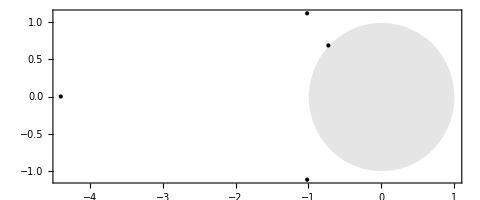

```mathematica
b0=b/.Solve[{-(b (1+b+b^2)^3)/(1+b)^8==1, Abs[b]>1||(Abs[b]==1&&Im[b]>0)},b]
Graphics[{Point[ReIm/@b0], Opacity[.1],Disk[]},
Axes->True,
Frame->True
]
```

```mathematica
ur0=ur/.s12/.{b->b0};
```

```mathematica
1/2/Pi N[a22/.{b->b0[[4]]}/.LiEval,100]
```

-0.523598775598298873077107230546583814032861566562517636829157432051302734381034833104672470890352845-1.157322100746665312432350757333190624833915687254350342447059385582416696939779140180935420831029923 ⅈ

```mathematica
a23=a22/.{Li2[x_]:>PolyLog[2,x]};
```

```mathematica
a24=Assuming[b>1,Simplify[a23]]
```

-3 Log[1-1/b^3] Log[b]+6 Log[1-1/b^2] Log[b]-3 Log[1-b] Log[b]-2 Log[(-1+b)/b] Log[b]+2 Log[b] Log[1-b^2]+PolyLog[2,1/b^3]-3 PolyLog[2,1/b^2]+2 PolyLog[2,1/b]-3 PolyLog[2,b]+PolyLog[2,b^2]

```mathematica
Simplify[D[b D[-a23/(2Pi), b], b]]
```

-((-1+b)^2 (-1-b+b^3+b^4+b (5+8 b+5 b^2) Log[b]))/(2 b (1+b)^2 (1+b+b^2)^2 π)

```mathematica
Simplify[D[b D[KerrDoranQ1[b], b], b]]
```

-((-1+b)^2 (-1-b+b^3+b^4+b (5+8 b+5 b^2) Log[b]))/(2 b (1+b)^2 (1+b+b^2)^2 π)

```mathematica
KerrDoranQ1[.001+1I]
```

0.523599-0.109527 ⅈ

```mathematica
KerrDoranQ1[.001+1I]
```

0.523599-0.109527 ⅈ

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2 Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[z]Log[1-z]}};
```

```mathematica
DeleteDuplicates[Cases[a22, Li2[__],Infinity]]
```

{Li2[1/b^3],Li2[1/b^2],Li2[b],Li2[b^2],Li2[1/b]}

```mathematica
rep={
Li2[1/b]->-π^2/6-Li2[b]-1/2 Log[-b]^2,
Li2[1/b^2]->-π^2/6-Li2[b^2]-1/2 Log[-b^2]^2,
Li2[1/b^3]->-π^2/6-Li2[b^3]-1/2 Log[-b^3]^2
};
```

```mathematica
a25=Simplify[Expand[-a22/.rep]]
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]+Log[-b]^2+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-3/2 Log[-b^2]^2+1/2 Log[-b^3]^2+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]+Log[1/b] Log[-(b (1+b+b^2))/(1+b)^4]+Log[b] Log[-(b (1+b+b^2))/(1+b)^4]+Log[1/b^2] Log[-(1+b+b^2)/(1+b)^2]-Log[1/b] Log[-(1+b+b^2)/(1+b)^2]+Log[b] Log[-(1+b+b^2)/(1+b)^2]

```mathematica
literms=a25/.{Log[_]:>0}
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]

```mathematica
extraterms=a25/.{Li2[_]:>0}
```

-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]+Log[-b]^2+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-3/2 Log[-b^2]^2+1/2 Log[-b^3]^2+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]+Log[1/b] Log[-(b (1+b+b^2))/(1+b)^4]+Log[b] Log[-(b (1+b+b^2))/(1+b)^4]+Log[1/b^2] Log[-(1+b+b^2)/(1+b)^2]-Log[1/b] Log[-(1+b+b^2)/(1+b)^2]+Log[b] Log[-(1+b+b^2)/(1+b)^2]

```mathematica
a26=literms+Assuming[Abs[b]>1, FullSimplify[extraterms]]
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]-(2 ArcTanh[1-2 b]+Log[-1+b]) Log[1/b]+Log[1-1/b^2] (2 Log[1/b^2]+Log[1/b]-Log[b])+(2 Log[1-b]-Log[-1+b]) Log[b]+Log[b]^2+Log[1-1/b^3] (-Log[1/b^2]+Log[b])+1/2 (-2 Log[1/b^2] Log[(-1+b)/b]+2 Log[-b]^2-3 Log[-b^2]^2+Log[-b^3]^2)+(Log[1/b]-Log[b]) Log[1-b^2]+(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
N[a26/(2Pi)/.{b->b0[[4]]}/.LiEval,100]
```

0.523598775598298873077107230546583814032861566562517636829157432051302734381034833104672470890352845+1.157322100746665312432350757333190624833915687254350342447059385582416696939779140180935420831029923 ⅈ

```mathematica
a27=literms+Assuming[b>1, FullSimplify[extraterms]]
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]+1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]

```mathematica
Simplify[D[b D[a27+K1+K2 Log[b]/.LiEval,b],b]]
```

-((-1+b)^2 (-1-b+b^3+b^4+b (5+8 b+5 b^2) Log[b]))/(b (1+b)^2 (1+b+b^2)^2)

```mathematica
b1=N[-a22/(2Pi)/.LiEval/.{b->b0[[4]]},20]
```

0.5235987755982988731+1.1573221007466653124 ⅈ

```mathematica
b2=Chop@N[a27/(2Pi)-Pi-5/2I Log[b]/.LiEval/.{b->b0[[4]]},20]
```

2.9056469608400944346+1.157322100746665312 ⅈ

```mathematica
b2=Chop@N[a27/(2Pi)+K1 Pi+K2 I Log[b]/.LiEval/.{b->b0[[4]]},20]
```

(0.09211915132539876923+1.1573221007466653124 ⅈ)+3.1415926535897932385 K1-2.3820481852417955615 K2

```mathematica
Chop@Simplify[(b1-b2)/Pi]
%/.First[s40]
```

0.137344230092931595-1. K1+0.758229486728621063 K2

First::normal: Nonatomic expression expected at position 1 in First[s40].

ReplaceAll::reps: {First[s40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.137344230092931595-1. K1+0.758229486728621063 K2/.First[s40]

```mathematica
b1=N[-a22/(2Pi)/.LiEval/.{b->b0[[3]]},20]
```

2.8818201527943000628+0.974278429399093013 ⅈ

```mathematica
b2=Chop@N[a27/(2Pi)-Pi-5/2I Log[b]/.LiEval/.{b->b0[[3]]},20]
ComplexExpand[ReIm[%]]
```

2.8818201527943000628+0.974278429399093013 ⅈ

{2.8818201527943000628,0.974278429399093013}

```mathematica
s40=Solve[{0.97427842939909301299126066804534670018`19.656030853787477==2.01133498064057183935473273036870658133`20.147021447054847+0.41482262049659153054538882492934402867`19.398437294148653 K2, 0.25614736712552737181026000681575084046`19.25202693647442+K1-2.30690617570342637176615728083241086394`20.1436047951461 K2==2.88182015279430006276300982561727489122`20.127014640533734}, {K1,K2}]
```

{{K1→-3.141592653589793238,K2→-2.5}}

```mathematica
N[b0[[4]]]
```

-0.72515+0.688591 ⅈ

```mathematica
N[KerrDoranQ2[b0[[4]]],20]
```

0.5235987755982988731+1.1573221007466653124 ⅈ

```mathematica
N[b0[[3]]]
```

-1.01658+1.12208 ⅈ

```mathematica
N[KerrDoranQ2[b0[[3]]],20]
```

0.7874250504011045705+0.97427842939909301299 ⅈ

```mathematica
ClearAll[b1,b2];
Plot3D[Im[a22/.LiEval/.{b->b1+I b2}], {b1,-4,4},{b2,-4,4}]
```

-Graphics3D-

```mathematica
ClearAll[b1,b2];
ComplexPlot[a22/.LiEval, {b,-2-2I,2+2I},
PlotPoints->80,MaxRecursion->4
]
```

-Graphics-

```mathematica
a27
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]+1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]

```mathematica
N[Log[el]/(2Pi I)/3/.s12/.{b->3/10+I 4/10},8]
```

0.16553293+0.1153051 ⅈ

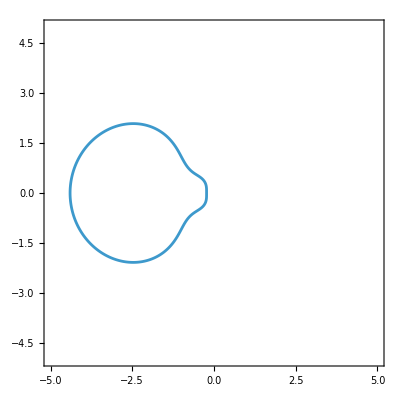

```mathematica
ComplexContourPlot[Abs[el/.s12]==1, {b,-5-5I, 5+5I},
PlotPoints->100,MaxRecursion->5,
Axes->True
]
```

```mathematica
Simplify[ComplexExpand[Abs[el/.s12/.{b->b1+I b2}]^2]]
```

((b1^2+b2^2) (1+2 b1^3+b1^4-b2^2+b2^4+2 b1 (1+b2^2)+b1^2 (3+2 b2^2))^3)/((1+2 b1+b1^2+b2^2)^8)

```mathematica
Simplify[Solve[(el/.s12)==Exp[2Pi I(3m)],b]]
```

{{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,1]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,2]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,3]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,4]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,5]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,6]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,7]},{b→Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,8]}}

```mathematica
cols=RandomColor[8]
```

{RGBColor[0.064211270047144, 0.8229742061628569, 0.5750274452704482],RGBColor[0.8800615965736045, 0.860329258206668, 0.9251072852919913],RGBColor[0.37167824820534245, 0.5024233213668674, 0.9932656323168114],RGBColor[0.33031795150244436, 0.29172029575504776, 0.5423571624192634],RGBColor[0.45514231208749956, 0.22396932107221001, 0.36111983439662465],RGBColor[0.7242441433579476, 0.21811960583856327, 0.36757017388735713],RGBColor[0.15798723513547897, 0.16455378168949464, 0.8263414174030086],RGBColor[0.885635532881085, 0.5979891501515078, 0.35949729988601575]}

```mathematica
Manipulate[Graphics[Table[{cols[[k]],PointSize[.02],Point[ReIm@
Root[ⅇ^(6 ⅈ m π)+(1+8 ⅇ^(6 ⅈ m π)) #1+(3+28 ⅇ^(6 ⅈ m π)) #1^2+(6+56 ⅇ^(6 ⅈ m π)) #1^3+(7+70 ⅇ^(6 ⅈ m π)) #1^4+(6+56 ⅇ^(6 ⅈ m π)) #1^5+(3+28 ⅇ^(6 ⅈ m π)) #1^6+(1+8 ⅇ^(6 ⅈ m π)) #1^7+ⅇ^(6 ⅈ m π) #1^8&,k]]},
 {k,8}],
PlotRange->{{-5,5},{-5,5}},
Axes->True,
Frame->True
], {{m,0},0,1/3,.001}]
```

```mathematica
FullSimplify[extraterms, Abs[b]>1&&Re[b]>0&&Im[b]>0]
```

1/2 (π^2+Log[-b^3]^2-2 Log[b] (3 ⅈ π-3 Log[-1+b]-12 Log[ⅈ b]+7 Log[b]+3 Log[b^3]+2 Log[1+b]+6 Log[-1+b^2]-3 Log[-1+b^3]))

```mathematica
Simplify[D[b D[-a22/.LiEval,b],b]]
```

-((-1+b)^2 (-1-b+b^3+b^4+b (5+8 b+5 b^2) Log[b]))/(b (1+b)^2 (1+b+b^2)^2)

```mathematica
Simplify[D[b D[a27/.LiEval,b],b]]
```

-((-1+b)^2 (-1-b+b^3+b^4+b (5+8 b+5 b^2) Log[b]))/(b (1+b)^2 (1+b+b^2)^2)

```mathematica
a27/.LiEval
```

1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]+5 PolyLog[2,b]-4 PolyLog[2,b^2]+PolyLog[2,b^3]

```mathematica
Plot3D[Re[(-a22-a27)]/.LiEval/.{b->b1+I b2}, {b1,-5,5},{b2,-5,5},
PlotPoints->100
]
```

$Aborted

```mathematica
FullSimplify[extraterms, Re[b]<0&&Im[b]>0&&Abs[b]>1]
```

2 Log[1-1/b^2] (Log[1/b^2]-Log[b])+Log[1-1/b^3] (-Log[1/b^2]+Log[b])+1/2 (π^2-2 Log[1/b^2] Log[(-1+b)/b]+Log[-b^3]^2+2 Log[b] (3 ⅈ π+Log[-1+b]-5 Log[b]-2 Log[1+b]))+(Log[1/b^2]+2 Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
Expand[extraterms/.{Log[-v_]:>Log[v]-I Pi}]/.{Log[v_^k_]:>k Log[v]}/.{Log[v_*k_]:>Log[v]+ Log[k]}/.{Log[v_^k_]:>k Log[v]}//Simplify
%/.{Log[1-1/b^3]->Log[-1+b]-3 Log[b]+Log[1+b+b^2], Log[1-1/b^2]->Log[-1+b]-2 Log[b]+Log[1+b]}//Simplify
%/.{Log[1-b^2]->Log[1-b]+Log[1+b]}//Simplify
%/.{2 Log[1-b]-2 Log[-1+b]->-2 ⅈ π}
```

1/2 Log[b] (2 ⅈ π+6 Log[1-1/b^3]-12 Log[1-1/b^2]+6 Log[1-b]+4 Log[-1+b]-5 Log[b]-4 Log[1-b^2])

1/2 Log[b] (2 ⅈ π+6 Log[1-b]-2 Log[-1+b]+Log[b]-12 Log[1+b]-4 Log[1-b^2]+6 Log[1+b+b^2])

1/2 Log[b] (2 ⅈ π+2 Log[1-b]-2 Log[-1+b]+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

1/2 Log[b] (Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

```mathematica
Expand[extraterms]/.{Log[v_^k_]:>k Log[v]}/.{Log[v_*k_]:>Log[v]+ Log[k]}/.{Log[v_^k_]:>k Log[v]}//Simplify
%/.{Log[1-1/b^3]->Log[-1+b]-3 Log[b]+Log[1+b+b^2], Log[1-1/b^2]->Log[-1+b]-2 Log[b]+Log[1+b]}//Simplify
%/.{Log[1-b^2]->Log[1-b]+Log[1+b]}//Simplify
%/.{2 Log[1-b]-2 Log[-1+b]->-2 ⅈ π}
```

-1/2 Log[b] (2 ⅈ π-6 Log[1-1/b^3]+12 Log[1-1/b^2]-6 Log[1-b]-4 Log[-1+b]+5 Log[b]+4 Log[1-b^2])

1/2 Log[b] (-2 ⅈ π+6 Log[1-b]-2 Log[-1+b]+Log[b]-12 Log[1+b]-4 Log[1-b^2]+6 Log[1+b+b^2])

1/2 Log[b] (-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

1/2 Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

```mathematica
Plot3D[Re[KerrDoranQ1[b]-(-a22/(2Pi)/.LiEval)]/.{b->b1+I b2}, {b1,-2,2},{b2,-2,2},
PlotPoints->50
]
```

-Graphics3D-

```mathematica
Plot3D[Re[KerrDoranQ2[b]-(-a22/(2Pi)/.LiEval)]/.{b->b1+I b2}, {b1,-2,2},{b2,-2,2},
PlotPoints->50
]
```

-Graphics3D-

```mathematica
ClearAll[temp];
temp[b1_]=KerrDoranQ1[b1]-(-a22/(2Pi)/.LiEval/.{b->b1});
```

```mathematica
complexGrid=RandomComplex[{0,10},50];
Chop[temp/@complexGrid]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
KerrDoranQ1[b]
```

(Log[b] (Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)+(5 PolyLog[2,b]-4 PolyLog[2,b^2]+PolyLog[2,b^3])/(2 π)

```mathematica
a27
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]+1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]

```mathematica
{a20[[2]],a21[[2]],a20[[1]],a21[[1]],Ab,Bb}/.{b->1}
```

{{1,1,1,1},{1,1,1},{1,1,-1,-1},{2,-1,-1},-3/16,-3/4}

```mathematica
{a20[[2]],a21[[2]],a20[[1]],a21[[1]],Ab,Bb}/.{b->1}
```

{{1,1,1,1},{1,1,1},{1,1,-1,-1},{2,-1,-1},-3/16,-3/4}

```mathematica
Simplify[KerrDoranFormulaExact[{1,1,1,1},{1,1,1},{1,1,-1,-1},{2,-1,-1},-3/16,-3/4]]
```

0

```mathematica
(-a22/(2Pi))-KerrDoranQ[b]//Simplify
Plot3D[Re[%/.LiEval]/.{b->b1+I b2}, {b1,-2,2},{b2,-2,2},
PlotPoints->50
]
```

-1/(6 π)(Log[1/b^2] (Log[2+1/b+b]-3 Log[-(1+b+b^2)/(1+b)^2])+Log[1/b] (3 Log[1/(2+1/b+b)^(2/3)]-Log[2+1/b+b]-3 Log[-(b (1+b+b^2))/(1+b)^4]+3 Log[-(1+b+b^2)/(1+b)^2])+Log[b] (3 Log[1/(2+1/b+b)^(2/3)]+Log[2+1/b+b]-3 (Log[-(b (1+b+b^2))/(1+b)^4]+Log[-(1+b+b^2)/(1+b)^2])))

-Graphics3D-

```mathematica
KerrDoranQ[b]
```

1/(6 π)(3 (Log[1/b]+Log[b]) Log[1/(2+1/b+b)^(2/3)]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[2+1/b+b]-3 (Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])-(Log[1/b]-Log[b]) Log[1-b^2]))

```mathematica
ExpandAll[(Sqrt[b]+1/Sqrt[b])^(2/3)]
```

(1/(√b)+√b)^(2/3)

```mathematica
Ab
```

-(b (1+b+b^2))/(1+b)^4

```mathematica
a27
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]+1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]

```mathematica
a22
```

Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])+(-Log[1/b]+Log[b]) Log[1-b^2]-(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]-(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
Simplify[KerrDoranFormula@@{a20[[2]],a21[[2]],a20[[1]],a21[[1]],E^t Ab,E^t Bb}-a22]
D[%,t]
```

(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]-(Log[1/b]+Log[b]) Log[-(b (1+b+b^2) ⅇ^t)/(1+b)^4]-(Log[1/b^2]-Log[1/b]+Log[b]) Log[-((1+b+b^2) ⅇ^t)/(1+b)^2]

-Log[1/b^2]-2 Log[b]

```mathematica
a30=Simplify[D[-a22/.LiEval, b]]
```

-((-1+b)^3 Log[b])/(b (1+b) (1+b+b^2))

```mathematica
a31=Simplify[D[a27/.LiEval, b]]
```

(-10 (1+2 b+2 b^2+b^3) Log[1-b]+(1-8 b+4 b^2-3 b^3) Log[b]+(1+2 b+2 b^2+b^3) (16 Log[1-b^2]+Log[(b (1+b+b^2)^6)/(1+b)^16]-6 Log[1-b^3]))/(2 b (1+b) (1+b+b^2))

```mathematica
Simplify[b Expand[a30-a31]]
Plot3D[Im[%]/.{b->b1+I b2}, {b1,-2,2},{b2,-2,2},
PlotPoints->60,
MaxRecursion->3,
PlotRange->{{-2,2},{-2,2},All}
]
```

1/2 (10 Log[1-b]+Log[b]-16 Log[1-b^2]-Log[(b (1+b+b^2)^6)/(1+b)^16]+6 Log[1-b^3])

-Graphics3D-

```mathematica
Simplify[b Expand[D[]]]
Manipulate[Plot[Im[%/.{b->b1+b2 I}], {b2, -50, 50},
PlotRange->{Automatic,All}
], {{b1,1},-50,50,.001}]
```

1/2 (10 Log[1-b]+Log[b]-16 Log[1-b^2]-Log[(b (1+b+b^2)^6)/(1+b)^16]+6 Log[1-b^3])

```mathematica
Simplify[b Expand[D[KerrDoranQ[b]-KerrDoranQ1[b]/.LiEval, b]]]
Manipulate[Plot[Im[%/.{b->b1+b2 I}], {b2, -50, 50},
PlotRange->{Automatic,All}
], {{b1,1},-50,50,.001}]
```

1/(6 (1+b) (1+b+b^2) π)(15 (1+2 b+2 b^2+b^3) Log[1-b]+(-1+b)^3 Log[1/b^2]-2 Log[b]+6 b Log[b]-6 b^2 Log[b]+2 b^3 Log[b]+24 Log[1+b]+48 b Log[1+b]+48 b^2 Log[1+b]+24 b^3 Log[1+b]-24 Log[1-b^2]-48 b Log[1-b^2]-48 b^2 Log[1-b^2]-24 b^3 Log[1-b^2]-9 Log[1+b+b^2]-18 b Log[1+b+b^2]-18 b^2 Log[1+b+b^2]-9 b^3 Log[1+b+b^2]+9 Log[1-b^3]+18 b Log[1-b^3]+18 b^2 Log[1-b^3]+9 b^3 Log[1-b^3])

```mathematica
a27
```

5 Li2[b]-4 Li2[b^2]+Li2[b^3]+1/2 Log[b] Log[(b (1+b+b^2)^6)/(1+b)^16]

Log[b]^2/2-8 Log[b] Log[1+b]+3 Log[b] Log[1+b+b^2]+5 PolyLog[2,b]-4 PolyLog[2,b^2]+PolyLog[2,b^3]

```mathematica
-a22
```

-Li2[1/b^3]+Li2[1/b^2]+Li2[b]-Li2[b^2]+2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])-Log[1-b] Log[1/b]-(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]-2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])-Log[1-1/b^3] (Log[1/b^2]-Log[b])+Log[1-1/b^2] (Log[1/b]-Log[b])-Log[(-1+b)/b] Log[b]+2 (Li2[b]+Log[1-b] Log[b])-(-Log[1/b]+Log[b]) Log[1-b^2]+(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]

```mathematica
Expand[2Pi KerrDoranQ1[b]]
```

Log[b]^2/2-8 Log[b] Log[1+b]+3 Log[b] Log[1+b+b^2]+5 PolyLog[2,b]-4 PolyLog[2,b^2]+PolyLog[2,b^3]

```mathematica
Simplify[b D[(-a22)-Expand[2Pi KerrDoranQ1[b]]/.LiEval, b]]
Manipulate[ReImPlot[%/.{b->b1+I b2}, {b2, -50,50},
PlotRange->All
], {{b1,1},-50,50,.001}]
```

5 Log[1-b]+8 Log[1+b]-8 Log[1-b^2]-3 Log[1+b+b^2]+3 Log[1-b^3]

```mathematica
Simplify[b D[Expand[2Pi KerrDoranQ[b]]-Expand[2Pi KerrDoranQ3[b]]/.LiEval, b]]
Manipulate[ReImPlot[%/.{b->b1+I b2}, {b2, -50,50},
PlotRange->All
], {{b1,1},-50,50,.001}]
```

1/(3 (1+b) (1+b+b^2))(-2 ⅈ π+6 ⅈ b π-6 ⅈ b^2 π+2 ⅈ b^3 π+15 (1+2 b+2 b^2+b^3) Log[1-b]+(-1+b)^3 Log[1/b^2]-2 Log[b]+6 b Log[b]-6 b^2 Log[b]+2 b^3 Log[b]+24 Log[1+b]+48 b Log[1+b]+48 b^2 Log[1+b]+24 b^3 Log[1+b]-24 Log[1-b^2]-48 b Log[1-b^2]-48 b^2 Log[1-b^2]-24 b^3 Log[1-b^2]-9 Log[1+b+b^2]-18 b Log[1+b+b^2]-18 b^2 Log[1+b+b^2]-9 b^3 Log[1+b+b^2]+9 Log[1-b^3]+18 b Log[1-b^3]+18 b^2 Log[1-b^3]+9 b^3 Log[1-b^3])

```mathematica
Simplify[Expand[2Pi KerrDoranQ[b]]-Expand[2Pi KerrDoranQ3[b]]/.LiEval]
Manipulate[ReImPlot[%/.{b->b1+I b2}, {b1, -50,50},
PlotRange->All
], {{b2,1},-50,50,.001}]
```

-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]-2/3 ⅈ π Log[b]+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-Log[b]^2/2+16/3 ⅈ π Log[1+b]+8 Log[b] Log[1+b]+Log[1/b] Log[1/(2+1/b+b)^(2/3)]+Log[b] Log[1/(2+1/b+b)^(2/3)]+1/3 Log[1/b^2] Log[2+1/b+b]-1/3 Log[1/b] Log[2+1/b+b]+1/3 Log[b] Log[2+1/b+b]+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]-2 ⅈ π Log[1+b+b^2]-3 Log[b] Log[1+b+b^2]-PolyLog[2,1/b^3]+3 PolyLog[2,1/b^2]-2 PolyLog[2,1/b]-2 PolyLog[2,b]+3 PolyLog[2,b^2]-PolyLog[2,b^3]

```mathematica
Simplify[D[b D[KerrDoranQ[b]-KerrDoranQ1[b]/.LiEval, b],b]]
Plot3D[Im[%]/.{b->b1+I b2}, {b1,-2,2},{b2,-2,2},
PlotRange->{{-2,2},{-2,2},All},
PlotPoints->60
]
```

((-1+b)^2 (5+8 b+5 b^2) (Log[1/b^2]+2 Log[b]))/(6 (1+b)^2 (1+b+b^2)^2 π)

-Graphics3D-

```mathematica
s31=Solve[{1==-(b (1+b+b^2)^3)/(1+b)^8, Abs[b]>1||Abs[b]==1&&Im[b]>0},b]
```

{{b→},{b→},{b→},{b→}}

```mathematica
ur0=ur/.s12/.s31;
Chop@N[ur0,10]
```

{-3.025715204,-0.2550986687-0.221552814 ⅈ,-0.2550986687+0.221552814 ⅈ,0.2631852692}

```mathematica
a40=Chop@N[(-a22/(2Pi))/.LiEval/.s31, 10]
```

{-0.9276276861,2.881820153-0.974278429 ⅈ,2.881820153+0.974278429 ⅈ,0.523598776+1.157322101 ⅈ}

```mathematica
Plot3D[Im[KerrDoranQ[b1+I b2]-KerrDoranQ3[b1+I b2]/.LiEval], {b1,-50,50},{b2,-50,50}]
```

-Graphics3D-

#### Interpreting Kerr Doran for other cusps

```mathematica
Chop[N[ur0]]
```

{-3.02572,-0.255099-0.221553 ⅈ,-0.255099+0.221553 ⅈ,0.263185}

```mathematica
upath=Interpolation[Thread[{{0, 1}, {I/10,ur0[[2]]+I*10^-20}}],InterpolationOrder->1]
```

InterpolatingFunction[…]

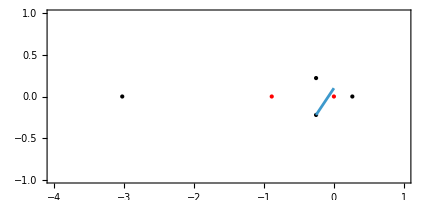

```mathematica
Show[{
Graphics[{Point[ReIm/@ur0], Red, Point[{ReIm[-8/9],ReIm[0]}]}],
ParametricPlot[ReIm[upath[t]],{t,0, 1}]
},
PlotRange->{{-4,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

```mathematica
Psi0=SystemMatrix2[F1Series2[1, upath[0], 512, 10], 1, upath[0]];
```

```mathematica
(*PsiRecord={};*)
```

```mathematica
wp=80; 
pg=50;
ag=Infinity;
sol=Monitor[NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA2[1,upath[t]].Psi[t],Psi[0]==Psi0},Psi,{t,0,1},
WorkingPrecision->40,
MaxSteps->Infinity,
StepMonitor:>(tt=t)
], ProgressIndicator[tt]];
Psi1=Psi[1]/. First[sol];
```

```mathematica
(*AppendTo[PsiRecord,Psi1];*)
```

```mathematica
tmp=Chop@TTDFromSystemMatrix[PsiRecord[[2]]]
```

{0.37532258908572061440142640351800413053+0.15506122798667381609103015956595618438 ⅈ,0.625967767257161843227203195166102935553+0.46518368396002144827535182869154594136 ⅈ}

```mathematica
tmp=Chop@TTDFromSystemMatrix[PsiRecord[[3]]]
```

{0.624677410914279385449365086431266903835+0.15506122798667381606243928031626753667 ⅈ,1.62338705457139692812558602586368899673+0.77530613993336908011984136287774549237 ⅈ}

```mathematica
tmp=Chop@TTDFromSystemMatrix[PsiRecord[[4]]]
```

{0.500000000000000000052103924999549841524,1.2690301350813831446483904793839241306}

```mathematica
Chop@N[ur0,10]
```

{-3.025715204,-0.2550986687-0.221552814 ⅈ,-0.2550986687+0.221552814 ⅈ,0.2631852692}

```mathematica
a40/(2Pi)
%[[3]]-tmp[[1]]
```

{-0.1476365316,0.4586559224-0.155061228 ⅈ,0.4586559224+0.155061228 ⅈ,0.0833333333+0.1841935331 ⅈ}

0.0833333333+0. ⅈ

```mathematica
a40/(2Pi)
%[[2]]+tmp[[1]]
```

{-0.1476365316,0.4586559224-0.155061228 ⅈ,0.4586559224+0.155061228 ⅈ,0.0833333333+0.1841935331 ⅈ}

1.083333333+0. ⅈ

```mathematica
a40/(2Pi)
%[[1]]-tmp[[2]]
Rationalize[%]
```

{-0.1476365316,0.4586559224-0.155061228 ⅈ,0.4586559224+0.155061228 ⅈ,0.0833333333+0.1841935331 ⅈ}

-1.4166666667

-17/12

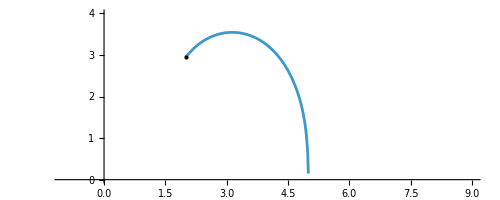

```mathematica
ParametricPlot[ReIm[TauFromSystemMatrix[Psi[t]/.First[sol]]], {t,0,1},
PlotRange->{{-1,9},{0,4}},
Epilog->{Point[ReIm[TauFromSystemMatrix[Psi[0]/.First[sol]]]]}
]
```

```mathematica
Ch[2,1].Sigma.Join[{1,0},TTDFromSystemMatrix[Psi1]]/.repCh
(*ComplexExpand[ReIm[%]]//Simplify
Solve[Thread[%==0],{p,q}]*)
```

-8.7876059370735447756×10^-19+1.92355038703592191×10^-19 ⅈ

```mathematica
Solve[el==(el/.s12),b]
```

{{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,1]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,2]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,3]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,4]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,5]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,6]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,7]},{b→Root[el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&,8]}}

```mathematica
el+(1+8 el) #1+(3+28 el) #1^2+(6+56 el) #1^3+(7+70 el) #1^4+(6+56 el) #1^5+(3+28 el) #1^6+(1+8 el) #1^7+el #1^8&[b]
%/.{b-}
```

el+b^8 el+b (1+8 el)+b^7 (1+8 el)+b^2 (3+28 el)+b^6 (3+28 el)+b^3 (6+56 el)+b^5 (6+56 el)+b^4 (7+70 el)

```mathematica
Simplify[ExpToTrig[(el/.s12/.b->Exp[t])]]
```

-1/256 (1+2 Cosh[t])^3 Sech[t/2]^8

```mathematica
FindIntegerNullVector[a40/(2Pi)]
```

{-4204+534 ⅈ,-13484+5074 ⅈ,-2030-4333 ⅈ,1088-26850 ⅈ}

```mathematica
a41=(-a22/(2Pi))/.LiEval/.s31;
```

```mathematica
FindIntegerNullVector[Chop[N[a41[[1;;2]]/(2Pi),100]]]
```

{2664334815776658330403608257231960685382489857617802223-12541286931621108389958170818480807051492610997200561366 ⅈ,1994450799631957232961710904538168149151299715262376179-3362629890215011960670189237283964578280376887491341160 ⅈ}

## Im(Q) = P?

```mathematica
el/.s12
```

-(b (1+b+b^2)^3)/(1+b)^8

```mathematica
KerrDoranP[b]
```

(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)

```mathematica
Simplify[KerrDoranP[b]-(1/2/Pi)(1/3)Log[Abs[-(b (1+b+b^2)^3)/(1+b)^8]](-3Arg[b])/.LiEval]
```

1/(2 π)(5 Im[PolyLog[2,b]]-4 Im[PolyLog[2,b^2]]+Im[PolyLog[2,b^3]]+5 Arg[1-b] Log[Abs[b]]-8 Arg[1-b^2] Log[Abs[b]]+3 Arg[1-b^3] Log[Abs[b]]+Arg[b] Log[Abs[(b (1+b+b^2)^3)/(1+b)^8]])

```mathematica
KerrDoranP1[b_]=KerrDoranP[b]-(1/2/Pi)(1/3)Log[Abs[-(b (1+b+b^2)^3)/(1+b)^8]](-3Arg[b])/.LiEval
```

(Im[PolyLog[2,b^3]]+5 (Im[PolyLog[2,b]]+Arg[1-b] Log[Abs[b]])-4 (Im[PolyLog[2,b^2]]+Arg[1-b^2] Log[Abs[b]^2])+Arg[1-b^3] Log[Abs[b]^3])/(2 π)+(Arg[b] Log[Abs[(b (1+b+b^2)^3)/(1+b)^8]])/(2 π)

```mathematica
Manipulate[Plot[{Im[(-a22/(2Pi))/.LiEval/.{b->b1+I b2}]-KerrDoranP1[b1+I b2]}, {b1,-10,10},
PlotRange->{Automatic,{-20,20}}
], {{b2,1/10},-10,10,.001}]
```

```mathematica
Log[Abs[-(b (1+b+b^2)^3)/(1+b)^8]]/.{b->b1+I b2}
```

Log[Abs[((b1+ⅈ b2) (1+b1+(b1+ⅈ b2)^2+ⅈ b2)^3)/(1+b1+ⅈ b2)^8]]

```mathematica
Manipulate[Plot[-3Log[Abs[((b1+ⅈ b2) (1+b1+(b1+ⅈ b2)^2+ⅈ b2)^3)/(1+b1+ⅈ b2)^8]], {b1,-50,50},
PlotRange->{Automatic,{-20,20}}
], {{b2,-24.595},-50,50,.001}]
```

```mathematica
Simplify[(-a22/(2Pi))/.LiEval]
N[%/.{b->b0[[4]]},100]
```

1/(2 π)(-Log[1-b] Log[1/b]-(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]-Log[1-1/b^3] (Log[1/b^2]-Log[b])+Log[1-1/b^2] (Log[1/b]-Log[b])-Log[(-1+b)/b] Log[b]+(Log[1/b]-Log[b]) Log[1-b^2]+(Log[1/b]+Log[b]) Log[-(b (1+b+b^2))/(1+b)^4]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[-(1+b+b^2)/(1+b)^2]-PolyLog[2,1/b^3]+PolyLog[2,1/b^2]+2 (Log[1-1/b^2] Log[1/b^2]+PolyLog[2,1/b^2])-2 (Log[1/b] Log[(-1+b)/b]+PolyLog[2,1/b])+PolyLog[2,b]+2 (Log[1-b] Log[b]+PolyLog[2,b])-PolyLog[2,b^2])

0.523598775598298873077107230546583814032861566562517636829157432051302734381034833104672470890352845+1.157322100746665312432350757333190624833915687254350342447059385582416696939779140180935420831029923 ⅈ

```mathematica
Simplify[(1/2/Pi)(1/3)Log[Abs[-(b (1+b+b^2)^3)/(1+b)^8]](-3Arg[b])]
```

-(Arg[b] Log[Abs[(b (1+b+b^2)^3)/(1+b)^8]])/(2 π)

```mathematica
KerrDoranP[b]
```

(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)

```mathematica
ClearAll[KerrDoranQNew, KerrDoranC, KerrDoranP0, KerrDoranPNew];
KerrDoranQNew[b_]:=1/(2 π)(-Log[1-b] Log[1/b]-(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]-Log[1-1/b^3] (Log[1/b^2]-Log[b])+Log[1-1/b^2] (Log[1/b]-Log[b])-Log[(-1+b)/b] Log[b]+(Log[1/b]-Log[b]) Log[1-b^2]+(Log[1/b]+Log[b]) Log[-((b (1+b+b^2))/(1+b)^4)]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[-((1+b+b^2)/(1+b)^2)]-PolyLog[2,1/b^3]+PolyLog[2,1/b^2]+2 (Log[1-1/b^2] Log[1/b^2]+PolyLog[2,1/b^2])-2 (Log[1/b] Log[(-1+b)/b]+PolyLog[2,1/b])+PolyLog[2,b]+2 (Log[1-b] Log[b]+PolyLog[2,b])-PolyLog[2,b^2]);
KerrDoranC[b_]:=((Arg[b] Log[Abs[(b (1+b+b^2)^3)/(1+b)^8]])/(2 π));
KerrDoranP0[b_]:=(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π);
KerrDoranPNew[b_]:=KerrDoranP0[b]+KerrDoranC[b];
```

```mathematica
Simplify[(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)/.LiEval]
```

(5 Im[PolyLog[2,b]]-4 Im[PolyLog[2,b^2]]+Im[PolyLog[2,b^3]]+5 Arg[1-b] Log[Abs[b]]-8 Arg[1-b^2] Log[Abs[b]]+3 Arg[1-b^3] Log[Abs[b]])/(2 π)

```mathematica
FNew[b_]:=1/(2 π)(5 Im[PolyLog[2,b]]-4 Im[PolyLog[2,b^2]]+Im[PolyLog[2,b^3]]+5 Arg[1-b] Log[Abs[b]]-8 Arg[1-b^2] Log[Abs[b]]+3 Arg[1-b^3] Log[Abs[b]]+Arg[b] Log[Abs[(b (1+b+b^2)^3)/(1+b)^8]]);
```

```mathematica
Simplify[KerrDoranPNew[b]/.LiEval]-FNew[b]//Simplify
```

0

```mathematica
Manipulate[Plot[Im[KerrDoranQNew[b1+I b2]]-KerrDoranPNew[b1+I b2]/.LiEval, {b1,-10,10},
PlotRange->{Automatic,{-20,20}}
], {{b2,1/10},-10,10,.001}]
```

```mathematica
Plot3D[Im[KerrDoranQNew[b1+I b2]]-KerrDoranPNew[b1+I b2]/.LiEval, {b1,-40,40},{b2,-40,40},
PlotRange->{Automatic,Automatic,{-2,2}}
]
```

-Graphics3D-

```mathematica
KerrDoranQ1[1]
```

π/6

## Picard Fuchs in terms of b and du

```mathematica
a1={KerrDoranElFromb[b], KerrDoranUrFromb[b]+du}
```

{-(b (1+b+b^2)^3)/(1+b)^8,-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du}

```mathematica
Series[MirrorCurveDelta2@@a1, {du,0,2}]//Simplify
```

((-1+b)^6 du)/((1+b)^2 (1+4 b+b^2)^2)+(2 b (1+b+b^2) (31+126 b+297 b^2+388 b^3+297 b^4+126 b^5+31 b^6) du^2)/((1+b)^8 (1+4 b+b^2))+O[du]^3

```mathematica
sol=Simplify[Solve[{-(b (1+b+b^2)^3)/(1+b)^8==el, -(1+b)^4/((1+b+b^2) (1+4 b+b^2))==ur+du},{b,du}]];
```

```mathematica
jac=Simplify[D[a1, {{b,du}}]]
jacI=Simplify[Inverse[%]]
```

{{((-1+b)^3 (1+b+b^2)^2)/(1+b)^9,0},{-((-1+b^2)^3)/((1+b+b^2)^2 (1+4 b+b^2)^2),1}}

{{(1+b)^9/((-1+b)^3 (1+b+b^2)^2),0},{(1+b)^12/((1+b+b^2)^4 (1+4 b+b^2)^2),1}}

```mathematica
rules={
Derivative[0,1][f][el,ur]->Derivative[0,1][G][b,du],
Derivative[0,2][f][el,ur]->Derivative[0,2][G][b,du],
Derivative[1,0][f][el,ur]->((1+b)^9 Derivative[1,0][G][b,du])/((-1+b)^3 (1+b+b^2)^2)+((1+b)^12 Derivative[0,1][G][b,du])/((1+b+b^2)^4 (1+4 b+b^2)^2),
Derivative[1,1][f][el,ur]->((1+b)^9 Derivative[1,1][G][b,du])/((-1+b)^3 (1+b+b^2)^2)+((1+b)^12 Derivative[0,2][G][b,du])/((1+b+b^2)^4 (1+4 b+b^2)^2),
Derivative[2,0][f][el,ur]->1/((1+4 b+b^2)^3 (-1+b^3)^7)(1+b)^17 (-12 (-1+b)^5 b (1+b)^3 Derivative[0,1][G][b,du]+(1+5 b+6 b^2+5 b^3+b^4) (2 (1+4 b+b^2)^2 (-5-6 b-10 b^2-4 b^3-3 b^4+b^5) Derivative[1,0][G][b,du]+(-1+b^2) ((-1+b^2)^3 Derivative[1,1][G][b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 Derivative[2,0][G][b,du])))+((1+b)^21 ((-1+b^2)^3 Derivative[0,2][G][b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 Derivative[1,1][G][b,du]))/((-1+b)^3 (1+b+b^2)^8 (1+4 b+b^2)^4)
};
```

```mathematica
a2=Simplify[PicardFuchsD1[f[el,ur],el,ur]/.rules/.{el->a1[[1]], ur->a1[[2]]}]
```

-2 (-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du)^3 G^(0,1)[b,du]-(-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du)^4 G^(0,2)[b,du]+(3 (1+b)^9 (((1+b)^3 G^(0,1)[b,du])/((1+4 b+b^2)^2)+((1+b+b^2)^2 G^(1,0)[b,du])/(-1+b)^3))/((1+b+b^2)^4)-((1+b)^9 (-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du) (((1+b)^3 G^(0,2)[b,du])/((1+4 b+b^2)^2)+((1+b+b^2)^2 G^(1,1)[b,du])/(-1+b)^3))/((1+b+b^2)^4)-(3 b (1+b)^13 ((-1+b^2)^3 G^(0,2)[b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 G^(1,1)[b,du]))/((-1+b)^3 (1+b+b^2)^5 (1+4 b+b^2)^4)-1/((1+4 b+b^2)^3 (-1+b^3)^7)3 b (1+b)^9 (1+b+b^2)^3 (-12 (-1+b)^5 b (1+b)^3 G^(0,1)[b,du]+(1+5 b+6 b^2+5 b^3+b^4) (2 (1+4 b+b^2)^2 (-5-6 b-10 b^2-4 b^3-3 b^4+b^5) G^(1,0)[b,du]+(-1+b^2) ((-1+b^2)^3 G^(1,1)[b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 G^(2,0)[b,du])))

```mathematica
a3=Simplify[PicardFuchsD2[f[el,ur],el,ur]/.rules/.{el->a1[[1]], ur->a1[[2]]}]
```

(-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du) (1-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du) G^(0,1)[b,du]+(-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du)^2 (1-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du) G^(0,2)[b,du]-1/((1+b+b^2)^2)b (1+b) (4 (1+b+b^2) (((1+b)^3 G^(0,1)[b,du])/((1+4 b+b^2)^2)+((1+b+b^2)^2 G^(1,0)[b,du])/(-1+b)^3)-(1+b+b^2) (-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du) (4+3 (-(1+b)^4/((1+b+b^2) (1+4 b+b^2))+du)) (((1+b)^3 G^(0,2)[b,du])/((1+4 b+b^2)^2)+((1+b+b^2)^2 G^(1,1)[b,du])/(-1+b)^3)+1/((1+4 b+b^2)^4)4 b (-((1+b)^4 ((-1+b^2)^3 G^(0,2)[b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 G^(1,1)[b,du]))/(-1+b)^3-1/((-1+b^3)^7)(1+b+b^2)^8 (1+4 b+b^2) (-12 (-1+b)^5 b (1+b)^3 G^(0,1)[b,du]+(1+5 b+6 b^2+5 b^3+b^4) (2 (1+4 b+b^2)^2 (-5-6 b-10 b^2-4 b^3-3 b^4+b^5) G^(1,0)[b,du]+(-1+b^2) ((-1+b^2)^3 G^(1,1)[b,du]+(1+5 b+6 b^2+5 b^3+b^4)^2 G^(2,0)[b,du])))))

```mathematica
Pi0=Series[G0[b]+du G1[b]+du^2 G2[b], {du,0,2}]
```

G0[b]+G1[b] du+G2[b] du^2+O[du]^3

```mathematica
Numerator[Simplify[Expand[a2]]]/.{G->Function[{b,du}, G0[b]+G1[b] du+G2[b] du^2+O[du]^3]};
a4=Simplify[%];
```

```mathematica
Numerator[Simplify[Expand[a3]]]/.{G->Function[{b,du}, G0[b]+G1[b] du+G2[b] du^2+O[du]^3]};
a5=Simplify[%];
```

```mathematica
Simplify@Coefficient[a4[[3,1]], G1[b]]
```

(-1+b)^5 (1+b)^12 (5+4 b+18 b^2+4 b^3+5 b^4)

```mathematica
Simplify@Coefficient[-(b+1)^6/b a5[[3,1]], G1[b]]
```

(-1+b)^5 (1+b)^12 (5+4 b+18 b^2+4 b^3+5 b^4)

```mathematica
Simplify@Coefficient[a4[[3,1]], G1'[b]]
```

(-1+b)^6 (1+b)^13 (1+5 b+6 b^2+5 b^3+b^4)

```mathematica
Simplify[Coefficient[-(b+1)^6/b a5[[3,1]], G1'[b]]]
```

(-1+b)^6 (1+b)^13 (1+5 b+6 b^2+5 b^3+b^4)

```mathematica
Simplify[a4[[3,1]]+(b+1)^6/b a5[[3,1]]]
```

(1+b)^7 (1+4 b+b^2)^3 (-1+b^3)^2 ((-1-6 b-8 b^2-4 b^3+b^4) G0'[b]+b (-1-b+b^3+b^4) G0''[b])

```mathematica
a6=(-1-6 b-8 b^2-4 b^3+b^4) G0'[b]+b (-1-b+b^3+b^4) G0''[b];
Coefficient[%,G0''[b]];
a7=Simplify[a6/%]
```

((-1-6 b-8 b^2-4 b^3+b^4) G0'[b])/(b (-1-b+b^3+b^4))+G0''[b]

## Picard Fuchs coefficients around I_1 fibers

```mathematica
MirrorCurveDelta2[el,#]
```

1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4

```mathematica
Simplify[Series[PicardFuchsP2[el,ur], {ur,0,2}]]
```

3/ur-1/8+(17/64-16 el) ur+(-217/512-84 el) ur^2+O[ur]^3

```mathematica
Simplify[Series[PicardFuchsQ2[el,ur], {ur,0,2}]]
```

1/ur^2-1/(8 ur)+(17/64-24 el)+(-217/512-(275 el)/2) ur+(2465/4096+(83 el)/16-80 el^2) ur^2+O[ur]^3

```mathematica
FullSimplify[Limit[(ur-Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1])PicardFuchsP2[el,ur], ur->Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]]]
```

1

```mathematica
p2=1/(ur-Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]) + (-102-4 (27+112 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]-2808 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2+36 el (-63+64 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^3)/(Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (8+9 Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]) (1-16 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]-108 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2+4 el (-27+16 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^3))+(4 (29111157+64 el (-597051+4 el (-40581+128 el (2019+128 el))))+2 Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (82904796-32 el (-18088677+16 el (2358315+32 el (-45063+4480 el)))+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (23914845-8 el (-252080181+256 el (1810836+el (-1250721+64 el (11295+512 el))))-432 el (-3129597+32 el (203391+8 el (-28917+32 el (1119+256 el)))) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1])))/((-27+16 el)^3 Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2 (-8+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (-9+128 el+4 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (252+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (459-128 el+9 (27-16 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]))))^2)(ur-Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1])^2;
```

```mathematica
a1=FullSimplify[Limit[(PicardFuchsP2[el,ur]-p2)/(ur-Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]), ur->Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]]]
Simplify[%/.{Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]->u0}]
```

-((2 (176061088890-96 el (-7594823331+16 el (1835380701+16 el (-172572525+32 el (4548339+32 el (63617+13824 el)))))+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (227803247532-64 el (-84931180533+64 el (4232927565+8 el (-649479951+8 el (47486331+16 el (-596079+32 el (12717+256 el))))))+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (52301766015+16 el (673724230371+32 el (-65445364827+16 el (4864279473+8 el (-446823783+16 el (18912447+800 el (20385+2048 el))))))+8 el (740360554479+64 el (-41195711997+16 el (2989355625+8 el (-518036877+8 el (75431817+32 el (4435479+32 el (32709+256 el))))))) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]))))/((-27+16 el)^5 Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1]^2 (8+9 Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1])^2 (1+4 el Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (-4+Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1] (-27+(-27+16 el) Root[1+#1-8 el #1^2-36 el #1^3+(-27 el+16 el^2) #1^4&,1])))^3))

-((2 (137438953472 el^8 u0^3+43046721 (4090+5292 u0+1215 u0^2)+536870912 el^7 u0 (-64+3200 u0+32709 u0^2)+452984832 el^6 (-768-3768 u0+37750 u0^2+164277 u0^3)+12754584 el (57164+426168 u0+845154 u0^2+464373 u0^3)-30233088 el^2 (93247+573480 u0+1108323 u0^2+697653 u0^3)+17915904 el^3 (236725+1187892 u0+2224179 u0^2+1366875 u0^3)-5308416 el^4 (673828+2345004 u0+5516343 u0^2+6395517 u0^3)+1572864 el^5 (-1017872+1589544 u0+12608298 u0^2+25143939 u0^3)))/((-27+16 el)^5 u0^2 (8+9 u0)^2 (1+64 el^2 u0^3-4 el u0 (4+27 u0+27 u0^2))^3))

```mathematica
Root[1+#1-8 el #1^2-36 el #1^3+el (-27+16 el) #1^4&,1]/.{el->1}
```

```mathematica
SumLimit[PicardFuchsP2[1,ur]-1/(ur-), ur->]
```

(-33+421 +3888 ^2+4824 ^3+1485 ^4)/(-8-34 +165 ^2+1440 ^3+2060 ^4+594 ^5)

```mathematica
GV[0,1,1/2].Sigma.{1,m,t,td}/.repCh
```

-1/2-m+t